# Task #3

```mathematica
FactorInteger[957260]
```

{{2,2},{5,1},{23,1},{2081,1}}

```mathematica
FactorInteger@600851475143
```

{{71,1},{839,1},{1471,1},{6857,1}}

```mathematica
FactorInteger[18446744073709551616]
```

{{2,64}}

```mathematica
FactorInteger[2^64-1]
```

{{3,1},{5,1},{17,1},{257,1},{641,1},{65537,1},{6700417,1}}

```mathematica
FactorInteger[2^128-1]
```

{{3,1},{5,1},{17,1},{257,1},{641,1},{65537,1},{274177,1},{6700417,1},{67280421310721,1}}

```mathematica
Sqrt[2^128-1]//N
```

1.84467×10^19

```mathematica
FactorInteger[2^64-1]
```

{{3,1},{5,1},{17,1},{257,1},{641,1},{65537,1},{6700417,1}}

```mathematica
2*1009*67280421310721
```

135771890205034978

```mathematica
Sqrt[15]//N
```

3.87298

```mathematica
15 === 3 5
```

True

# Task #4 Palindrome numbers

```mathematica
9009
```

```mathematica
BaseForm[9009,2]
```

10001100110001_2

```mathematica
BaseForm[9119,2]
```

10001110011111_2

```mathematica
BaseForm[89998,2]
```

10101111110001110_2

```mathematica
BaseForm[899798,2]
```

11011011101011010110_2

```mathematica
Array[Times[#1 #2]&,{99,99}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126 | 128 | 130 | 132 | 134 | 136 | 138 | 140 | 142 | 144 | 146 | 148 | 150 | 152 | 154 | 156 | 158 | 160 | 162 | 164 | 166 | 168 | 170 | 172 | 174 | 176 | 178 | 180 | 182 | 184 | 186 | 188 | 190 | 192 | 194 | 196 | 198
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36 | 39 | 42 | 45 | 48 | 51 | 54 | 57 | 60 | 63 | 66 | 69 | 72 | 75 | 78 | 81 | 84 | 87 | 90 | 93 | 96 | 99 | 102 | 105 | 108 | 111 | 114 | 117 | 120 | 123 | 126 | 129 | 132 | 135 | 138 | 141 | 144 | 147 | 150 | 153 | 156 | 159 | 162 | 165 | 168 | 171 | 174 | 177 | 180 | 183 | 186 | 189 | 192 | 195 | 198 | 201 | 204 | 207 | 210 | 213 | 216 | 219 | 222 | 225 | 228 | 231 | 234 | 237 | 240 | 243 | 246 | 249 | 252 | 255 | 258 | 261 | 264 | 267 | 270 | 273 | 276 | 279 | 282 | 285 | 288 | 291 | 294 | 297
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48 | 52 | 56 | 60 | 64 | 68 | 72 | 76 | 80 | 84 | 88 | 92 | 96 | 100 | 104 | 108 | 112 | 116 | 120 | 124 | 128 | 132 | 136 | 140 | 144 | 148 | 152 | 156 | 160 | 164 | 168 | 172 | 176 | 180 | 184 | 188 | 192 | 196 | 200 | 204 | 208 | 212 | 216 | 220 | 224 | 228 | 232 | 236 | 240 | 244 | 248 | 252 | 256 | 260 | 264 | 268 | 272 | 276 | 280 | 284 | 288 | 292 | 296 | 300 | 304 | 308 | 312 | 316 | 320 | 324 | 328 | 332 | 336 | 340 | 344 | 348 | 352 | 356 | 360 | 364 | 368 | 372 | 376 | 380 | 384 | 388 | 392 | 396
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80 | 85 | 90 | 95 | 100 | 105 | 110 | 115 | 120 | 125 | 130 | 135 | 140 | 145 | 150 | 155 | 160 | 165 | 170 | 175 | 180 | 185 | 190 | 195 | 200 | 205 | 210 | 215 | 220 | 225 | 230 | 235 | 240 | 245 | 250 | 255 | 260 | 265 | 270 | 275 | 280 | 285 | 290 | 295 | 300 | 305 | 310 | 315 | 320 | 325 | 330 | 335 | 340 | 345 | 350 | 355 | 360 | 365 | 370 | 375 | 380 | 385 | 390 | 395 | 400 | 405 | 410 | 415 | 420 | 425 | 430 | 435 | 440 | 445 | 450 | 455 | 460 | 465 | 470 | 475 | 480 | 485 | 490 | 495
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72 | 78 | 84 | 90 | 96 | 102 | 108 | 114 | 120 | 126 | 132 | 138 | 144 | 150 | 156 | 162 | 168 | 174 | 180 | 186 | 192 | 198 | 204 | 210 | 216 | 222 | 228 | 234 | 240 | 246 | 252 | 258 | 264 | 270 | 276 | 282 | 288 | 294 | 300 | 306 | 312 | 318 | 324 | 330 | 336 | 342 | 348 | 354 | 360 | 366 | 372 | 378 | 384 | 390 | 396 | 402 | 408 | 414 | 420 | 426 | 432 | 438 | 444 | 450 | 456 | 462 | 468 | 474 | 480 | 486 | 492 | 498 | 504 | 510 | 516 | 522 | 528 | 534 | 540 | 546 | 552 | 558 | 564 | 570 | 576 | 582 | 588 | 594
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84 | 91 | 98 | 105 | 112 | 119 | 126 | 133 | 140 | 147 | 154 | 161 | 168 | 175 | 182 | 189 | 196 | 203 | 210 | 217 | 224 | 231 | 238 | 245 | 252 | 259 | 266 | 273 | 280 | 287 | 294 | 301 | 308 | 315 | 322 | 329 | 336 | 343 | 350 | 357 | 364 | 371 | 378 | 385 | 392 | 399 | 406 | 413 | 420 | 427 | 434 | 441 | 448 | 455 | 462 | 469 | 476 | 483 | 490 | 497 | 504 | 511 | 518 | 525 | 532 | 539 | 546 | 553 | 560 | 567 | 574 | 581 | 588 | 595 | 602 | 609 | 616 | 623 | 630 | 637 | 644 | 651 | 658 | 665 | 672 | 679 | 686 | 693
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96 | 104 | 112 | 120 | 128 | 136 | 144 | 152 | 160 | 168 | 176 | 184 | 192 | 200 | 208 | 216 | 224 | 232 | 240 | 248 | 256 | 264 | 272 | 280 | 288 | 296 | 304 | 312 | 320 | 328 | 336 | 344 | 352 | 360 | 368 | 376 | 384 | 392 | 400 | 408 | 416 | 424 | 432 | 440 | 448 | 456 | 464 | 472 | 480 | 488 | 496 | 504 | 512 | 520 | 528 | 536 | 544 | 552 | 560 | 568 | 576 | 584 | 592 | 600 | 608 | 616 | 624 | 632 | 640 | 648 | 656 | 664 | 672 | 680 | 688 | 696 | 704 | 712 | 720 | 728 | 736 | 744 | 752 | 760 | 768 | 776 | 784 | 792
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108 | 117 | 126 | 135 | 144 | 153 | 162 | 171 | 180 | 189 | 198 | 207 | 216 | 225 | 234 | 243 | 252 | 261 | 270 | 279 | 288 | 297 | 306 | 315 | 324 | 333 | 342 | 351 | 360 | 369 | 378 | 387 | 396 | 405 | 414 | 423 | 432 | 441 | 450 | 459 | 468 | 477 | 486 | 495 | 504 | 513 | 522 | 531 | 540 | 549 | 558 | 567 | 576 | 585 | 594 | 603 | 612 | 621 | 630 | 639 | 648 | 657 | 666 | 675 | 684 | 693 | 702 | 711 | 720 | 729 | 738 | 747 | 756 | 765 | 774 | 783 | 792 | 801 | 810 | 819 | 828 | 837 | 846 | 855 | 864 | 873 | 882 | 891
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120 | 130 | 140 | 150 | 160 | 170 | 180 | 190 | 200 | 210 | 220 | 230 | 240 | 250 | 260 | 270 | 280 | 290 | 300 | 310 | 320 | 330 | 340 | 350 | 360 | 370 | 380 | 390 | 400 | 410 | 420 | 430 | 440 | 450 | 460 | 470 | 480 | 490 | 500 | 510 | 520 | 530 | 540 | 550 | 560 | 570 | 580 | 590 | 600 | 610 | 620 | 630 | 640 | 650 | 660 | 670 | 680 | 690 | 700 | 710 | 720 | 730 | 740 | 750 | 760 | 770 | 780 | 790 | 800 | 810 | 820 | 830 | 840 | 850 | 860 | 870 | 880 | 890 | 900 | 910 | 920 | 930 | 940 | 950 | 960 | 970 | 980 | 990
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132 | 143 | 154 | 165 | 176 | 187 | 198 | 209 | 220 | 231 | 242 | 253 | 264 | 275 | 286 | 297 | 308 | 319 | 330 | 341 | 352 | 363 | 374 | 385 | 396 | 407 | 418 | 429 | 440 | 451 | 462 | 473 | 484 | 495 | 506 | 517 | 528 | 539 | 550 | 561 | 572 | 583 | 594 | 605 | 616 | 627 | 638 | 649 | 660 | 671 | 682 | 693 | 704 | 715 | 726 | 737 | 748 | 759 | 770 | 781 | 792 | 803 | 814 | 825 | 836 | 847 | 858 | 869 | 880 | 891 | 902 | 913 | 924 | 935 | 946 | 957 | 968 | 979 | 990 | 1001 | 1012 | 1023 | 1034 | 1045 | 1056 | 1067 | 1078 | 1089
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144 | 156 | 168 | 180 | 192 | 204 | 216 | 228 | 240 | 252 | 264 | 276 | 288 | 300 | 312 | 324 | 336 | 348 | 360 | 372 | 384 | 396 | 408 | 420 | 432 | 444 | 456 | 468 | 480 | 492 | 504 | 516 | 528 | 540 | 552 | 564 | 576 | 588 | 600 | 612 | 624 | 636 | 648 | 660 | 672 | 684 | 696 | 708 | 720 | 732 | 744 | 756 | 768 | 780 | 792 | 804 | 816 | 828 | 840 | 852 | 864 | 876 | 888 | 900 | 912 | 924 | 936 | 948 | 960 | 972 | 984 | 996 | 1008 | 1020 | 1032 | 1044 | 1056 | 1068 | 1080 | 1092 | 1104 | 1116 | 1128 | 1140 | 1152 | 1164 | 1176 | 1188
13 | 26 | 39 | 52 | 65 | 78 | 91 | 104 | 117 | 130 | 143 | 156 | 169 | 182 | 195 | 208 | 221 | 234 | 247 | 260 | 273 | 286 | 299 | 312 | 325 | 338 | 351 | 364 | 377 | 390 | 403 | 416 | 429 | 442 | 455 | 468 | 481 | 494 | 507 | 520 | 533 | 546 | 559 | 572 | 585 | 598 | 611 | 624 | 637 | 650 | 663 | 676 | 689 | 702 | 715 | 728 | 741 | 754 | 767 | 780 | 793 | 806 | 819 | 832 | 845 | 858 | 871 | 884 | 897 | 910 | 923 | 936 | 949 | 962 | 975 | 988 | 1001 | 1014 | 1027 | 1040 | 1053 | 1066 | 1079 | 1092 | 1105 | 1118 | 1131 | 1144 | 1157 | 1170 | 1183 | 1196 | 1209 | 1222 | 1235 | 1248 | 1261 | 1274 | 1287
14 | 28 | 42 | 56 | 70 | 84 | 98 | 112 | 126 | 140 | 154 | 168 | 182 | 196 | 210 | 224 | 238 | 252 | 266 | 280 | 294 | 308 | 322 | 336 | 350 | 364 | 378 | 392 | 406 | 420 | 434 | 448 | 462 | 476 | 490 | 504 | 518 | 532 | 546 | 560 | 574 | 588 | 602 | 616 | 630 | 644 | 658 | 672 | 686 | 700 | 714 | 728 | 742 | 756 | 770 | 784 | 798 | 812 | 826 | 840 | 854 | 868 | 882 | 896 | 910 | 924 | 938 | 952 | 966 | 980 | 994 | 1008 | 1022 | 1036 | 1050 | 1064 | 1078 | 1092 | 1106 | 1120 | 1134 | 1148 | 1162 | 1176 | 1190 | 1204 | 1218 | 1232 | 1246 | 1260 | 1274 | 1288 | 1302 | 1316 | 1330 | 1344 | 1358 | 1372 | 1386
15 | 30 | 45 | 60 | 75 | 90 | 105 | 120 | 135 | 150 | 165 | 180 | 195 | 210 | 225 | 240 | 255 | 270 | 285 | 300 | 315 | 330 | 345 | 360 | 375 | 390 | 405 | 420 | 435 | 450 | 465 | 480 | 495 | 510 | 525 | 540 | 555 | 570 | 585 | 600 | 615 | 630 | 645 | 660 | 675 | 690 | 705 | 720 | 735 | 750 | 765 | 780 | 795 | 810 | 825 | 840 | 855 | 870 | 885 | 900 | 915 | 930 | 945 | 960 | 975 | 990 | 1005 | 1020 | 1035 | 1050 | 1065 | 1080 | 1095 | 1110 | 1125 | 1140 | 1155 | 1170 | 1185 | 1200 | 1215 | 1230 | 1245 | 1260 | 1275 | 1290 | 1305 | 1320 | 1335 | 1350 | 1365 | 1380 | 1395 | 1410 | 1425 | 1440 | 1455 | 1470 | 1485
16 | 32 | 48 | 64 | 80 | 96 | 112 | 128 | 144 | 160 | 176 | 192 | 208 | 224 | 240 | 256 | 272 | 288 | 304 | 320 | 336 | 352 | 368 | 384 | 400 | 416 | 432 | 448 | 464 | 480 | 496 | 512 | 528 | 544 | 560 | 576 | 592 | 608 | 624 | 640 | 656 | 672 | 688 | 704 | 720 | 736 | 752 | 768 | 784 | 800 | 816 | 832 | 848 | 864 | 880 | 896 | 912 | 928 | 944 | 960 | 976 | 992 | 1008 | 1024 | 1040 | 1056 | 1072 | 1088 | 1104 | 1120 | 1136 | 1152 | 1168 | 1184 | 1200 | 1216 | 1232 | 1248 | 1264 | 1280 | 1296 | 1312 | 1328 | 1344 | 1360 | 1376 | 1392 | 1408 | 1424 | 1440 | 1456 | 1472 | 1488 | 1504 | 1520 | 1536 | 1552 | 1568 | 1584
17 | 34 | 51 | 68 | 85 | 102 | 119 | 136 | 153 | 170 | 187 | 204 | 221 | 238 | 255 | 272 | 289 | 306 | 323 | 340 | 357 | 374 | 391 | 408 | 425 | 442 | 459 | 476 | 493 | 510 | 527 | 544 | 561 | 578 | 595 | 612 | 629 | 646 | 663 | 680 | 697 | 714 | 731 | 748 | 765 | 782 | 799 | 816 | 833 | 850 | 867 | 884 | 901 | 918 | 935 | 952 | 969 | 986 | 1003 | 1020 | 1037 | 1054 | 1071 | 1088 | 1105 | 1122 | 1139 | 1156 | 1173 | 1190 | 1207 | 1224 | 1241 | 1258 | 1275 | 1292 | 1309 | 1326 | 1343 | 1360 | 1377 | 1394 | 1411 | 1428 | 1445 | 1462 | 1479 | 1496 | 1513 | 1530 | 1547 | 1564 | 1581 | 1598 | 1615 | 1632 | 1649 | 1666 | 1683
18 | 36 | 54 | 72 | 90 | 108 | 126 | 144 | 162 | 180 | 198 | 216 | 234 | 252 | 270 | 288 | 306 | 324 | 342 | 360 | 378 | 396 | 414 | 432 | 450 | 468 | 486 | 504 | 522 | 540 | 558 | 576 | 594 | 612 | 630 | 648 | 666 | 684 | 702 | 720 | 738 | 756 | 774 | 792 | 810 | 828 | 846 | 864 | 882 | 900 | 918 | 936 | 954 | 972 | 990 | 1008 | 1026 | 1044 | 1062 | 1080 | 1098 | 1116 | 1134 | 1152 | 1170 | 1188 | 1206 | 1224 | 1242 | 1260 | 1278 | 1296 | 1314 | 1332 | 1350 | 1368 | 1386 | 1404 | 1422 | 1440 | 1458 | 1476 | 1494 | 1512 | 1530 | 1548 | 1566 | 1584 | 1602 | 1620 | 1638 | 1656 | 1674 | 1692 | 1710 | 1728 | 1746 | 1764 | 1782
19 | 38 | 57 | 76 | 95 | 114 | 133 | 152 | 171 | 190 | 209 | 228 | 247 | 266 | 285 | 304 | 323 | 342 | 361 | 380 | 399 | 418 | 437 | 456 | 475 | 494 | 513 | 532 | 551 | 570 | 589 | 608 | 627 | 646 | 665 | 684 | 703 | 722 | 741 | 760 | 779 | 798 | 817 | 836 | 855 | 874 | 893 | 912 | 931 | 950 | 969 | 988 | 1007 | 1026 | 1045 | 1064 | 1083 | 1102 | 1121 | 1140 | 1159 | 1178 | 1197 | 1216 | 1235 | 1254 | 1273 | 1292 | 1311 | 1330 | 1349 | 1368 | 1387 | 1406 | 1425 | 1444 | 1463 | 1482 | 1501 | 1520 | 1539 | 1558 | 1577 | 1596 | 1615 | 1634 | 1653 | 1672 | 1691 | 1710 | 1729 | 1748 | 1767 | 1786 | 1805 | 1824 | 1843 | 1862 | 1881
20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 | 420 | 440 | 460 | 480 | 500 | 520 | 540 | 560 | 580 | 600 | 620 | 640 | 660 | 680 | 700 | 720 | 740 | 760 | 780 | 800 | 820 | 840 | 860 | 880 | 900 | 920 | 940 | 960 | 980 | 1000 | 1020 | 1040 | 1060 | 1080 | 1100 | 1120 | 1140 | 1160 | 1180 | 1200 | 1220 | 1240 | 1260 | 1280 | 1300 | 1320 | 1340 | 1360 | 1380 | 1400 | 1420 | 1440 | 1460 | 1480 | 1500 | 1520 | 1540 | 1560 | 1580 | 1600 | 1620 | 1640 | 1660 | 1680 | 1700 | 1720 | 1740 | 1760 | 1780 | 1800 | 1820 | 1840 | 1860 | 1880 | 1900 | 1920 | 1940 | 1960 | 1980
21 | 42 | 63 | 84 | 105 | 126 | 147 | 168 | 189 | 210 | 231 | 252 | 273 | 294 | 315 | 336 | 357 | 378 | 399 | 420 | 441 | 462 | 483 | 504 | 525 | 546 | 567 | 588 | 609 | 630 | 651 | 672 | 693 | 714 | 735 | 756 | 777 | 798 | 819 | 840 | 861 | 882 | 903 | 924 | 945 | 966 | 987 | 1008 | 1029 | 1050 | 1071 | 1092 | 1113 | 1134 | 1155 | 1176 | 1197 | 1218 | 1239 | 1260 | 1281 | 1302 | 1323 | 1344 | 1365 | 1386 | 1407 | 1428 | 1449 | 1470 | 1491 | 1512 | 1533 | 1554 | 1575 | 1596 | 1617 | 1638 | 1659 | 1680 | 1701 | 1722 | 1743 | 1764 | 1785 | 1806 | 1827 | 1848 | 1869 | 1890 | 1911 | 1932 | 1953 | 1974 | 1995 | 2016 | 2037 | 2058 | 2079
22 | 44 | 66 | 88 | 110 | 132 | 154 | 176 | 198 | 220 | 242 | 264 | 286 | 308 | 330 | 352 | 374 | 396 | 418 | 440 | 462 | 484 | 506 | 528 | 550 | 572 | 594 | 616 | 638 | 660 | 682 | 704 | 726 | 748 | 770 | 792 | 814 | 836 | 858 | 880 | 902 | 924 | 946 | 968 | 990 | 1012 | 1034 | 1056 | 1078 | 1100 | 1122 | 1144 | 1166 | 1188 | 1210 | 1232 | 1254 | 1276 | 1298 | 1320 | 1342 | 1364 | 1386 | 1408 | 1430 | 1452 | 1474 | 1496 | 1518 | 1540 | 1562 | 1584 | 1606 | 1628 | 1650 | 1672 | 1694 | 1716 | 1738 | 1760 | 1782 | 1804 | 1826 | 1848 | 1870 | 1892 | 1914 | 1936 | 1958 | 1980 | 2002 | 2024 | 2046 | 2068 | 2090 | 2112 | 2134 | 2156 | 2178
23 | 46 | 69 | 92 | 115 | 138 | 161 | 184 | 207 | 230 | 253 | 276 | 299 | 322 | 345 | 368 | 391 | 414 | 437 | 460 | 483 | 506 | 529 | 552 | 575 | 598 | 621 | 644 | 667 | 690 | 713 | 736 | 759 | 782 | 805 | 828 | 851 | 874 | 897 | 920 | 943 | 966 | 989 | 1012 | 1035 | 1058 | 1081 | 1104 | 1127 | 1150 | 1173 | 1196 | 1219 | 1242 | 1265 | 1288 | 1311 | 1334 | 1357 | 1380 | 1403 | 1426 | 1449 | 1472 | 1495 | 1518 | 1541 | 1564 | 1587 | 1610 | 1633 | 1656 | 1679 | 1702 | 1725 | 1748 | 1771 | 1794 | 1817 | 1840 | 1863 | 1886 | 1909 | 1932 | 1955 | 1978 | 2001 | 2024 | 2047 | 2070 | 2093 | 2116 | 2139 | 2162 | 2185 | 2208 | 2231 | 2254 | 2277
24 | 48 | 72 | 96 | 120 | 144 | 168 | 192 | 216 | 240 | 264 | 288 | 312 | 336 | 360 | 384 | 408 | 432 | 456 | 480 | 504 | 528 | 552 | 576 | 600 | 624 | 648 | 672 | 696 | 720 | 744 | 768 | 792 | 816 | 840 | 864 | 888 | 912 | 936 | 960 | 984 | 1008 | 1032 | 1056 | 1080 | 1104 | 1128 | 1152 | 1176 | 1200 | 1224 | 1248 | 1272 | 1296 | 1320 | 1344 | 1368 | 1392 | 1416 | 1440 | 1464 | 1488 | 1512 | 1536 | 1560 | 1584 | 1608 | 1632 | 1656 | 1680 | 1704 | 1728 | 1752 | 1776 | 1800 | 1824 | 1848 | 1872 | 1896 | 1920 | 1944 | 1968 | 1992 | 2016 | 2040 | 2064 | 2088 | 2112 | 2136 | 2160 | 2184 | 2208 | 2232 | 2256 | 2280 | 2304 | 2328 | 2352 | 2376
25 | 50 | 75 | 100 | 125 | 150 | 175 | 200 | 225 | 250 | 275 | 300 | 325 | 350 | 375 | 400 | 425 | 450 | 475 | 500 | 525 | 550 | 575 | 600 | 625 | 650 | 675 | 700 | 725 | 750 | 775 | 800 | 825 | 850 | 875 | 900 | 925 | 950 | 975 | 1000 | 1025 | 1050 | 1075 | 1100 | 1125 | 1150 | 1175 | 1200 | 1225 | 1250 | 1275 | 1300 | 1325 | 1350 | 1375 | 1400 | 1425 | 1450 | 1475 | 1500 | 1525 | 1550 | 1575 | 1600 | 1625 | 1650 | 1675 | 1700 | 1725 | 1750 | 1775 | 1800 | 1825 | 1850 | 1875 | 1900 | 1925 | 1950 | 1975 | 2000 | 2025 | 2050 | 2075 | 2100 | 2125 | 2150 | 2175 | 2200 | 2225 | 2250 | 2275 | 2300 | 2325 | 2350 | 2375 | 2400 | 2425 | 2450 | 2475
26 | 52 | 78 | 104 | 130 | 156 | 182 | 208 | 234 | 260 | 286 | 312 | 338 | 364 | 390 | 416 | 442 | 468 | 494 | 520 | 546 | 572 | 598 | 624 | 650 | 676 | 702 | 728 | 754 | 780 | 806 | 832 | 858 | 884 | 910 | 936 | 962 | 988 | 1014 | 1040 | 1066 | 1092 | 1118 | 1144 | 1170 | 1196 | 1222 | 1248 | 1274 | 1300 | 1326 | 1352 | 1378 | 1404 | 1430 | 1456 | 1482 | 1508 | 1534 | 1560 | 1586 | 1612 | 1638 | 1664 | 1690 | 1716 | 1742 | 1768 | 1794 | 1820 | 1846 | 1872 | 1898 | 1924 | 1950 | 1976 | 2002 | 2028 | 2054 | 2080 | 2106 | 2132 | 2158 | 2184 | 2210 | 2236 | 2262 | 2288 | 2314 | 2340 | 2366 | 2392 | 2418 | 2444 | 2470 | 2496 | 2522 | 2548 | 2574
27 | 54 | 81 | 108 | 135 | 162 | 189 | 216 | 243 | 270 | 297 | 324 | 351 | 378 | 405 | 432 | 459 | 486 | 513 | 540 | 567 | 594 | 621 | 648 | 675 | 702 | 729 | 756 | 783 | 810 | 837 | 864 | 891 | 918 | 945 | 972 | 999 | 1026 | 1053 | 1080 | 1107 | 1134 | 1161 | 1188 | 1215 | 1242 | 1269 | 1296 | 1323 | 1350 | 1377 | 1404 | 1431 | 1458 | 1485 | 1512 | 1539 | 1566 | 1593 | 1620 | 1647 | 1674 | 1701 | 1728 | 1755 | 1782 | 1809 | 1836 | 1863 | 1890 | 1917 | 1944 | 1971 | 1998 | 2025 | 2052 | 2079 | 2106 | 2133 | 2160 | 2187 | 2214 | 2241 | 2268 | 2295 | 2322 | 2349 | 2376 | 2403 | 2430 | 2457 | 2484 | 2511 | 2538 | 2565 | 2592 | 2619 | 2646 | 2673
28 | 56 | 84 | 112 | 140 | 168 | 196 | 224 | 252 | 280 | 308 | 336 | 364 | 392 | 420 | 448 | 476 | 504 | 532 | 560 | 588 | 616 | 644 | 672 | 700 | 728 | 756 | 784 | 812 | 840 | 868 | 896 | 924 | 952 | 980 | 1008 | 1036 | 1064 | 1092 | 1120 | 1148 | 1176 | 1204 | 1232 | 1260 | 1288 | 1316 | 1344 | 1372 | 1400 | 1428 | 1456 | 1484 | 1512 | 1540 | 1568 | 1596 | 1624 | 1652 | 1680 | 1708 | 1736 | 1764 | 1792 | 1820 | 1848 | 1876 | 1904 | 1932 | 1960 | 1988 | 2016 | 2044 | 2072 | 2100 | 2128 | 2156 | 2184 | 2212 | 2240 | 2268 | 2296 | 2324 | 2352 | 2380 | 2408 | 2436 | 2464 | 2492 | 2520 | 2548 | 2576 | 2604 | 2632 | 2660 | 2688 | 2716 | 2744 | 2772
29 | 58 | 87 | 116 | 145 | 174 | 203 | 232 | 261 | 290 | 319 | 348 | 377 | 406 | 435 | 464 | 493 | 522 | 551 | 580 | 609 | 638 | 667 | 696 | 725 | 754 | 783 | 812 | 841 | 870 | 899 | 928 | 957 | 986 | 1015 | 1044 | 1073 | 1102 | 1131 | 1160 | 1189 | 1218 | 1247 | 1276 | 1305 | 1334 | 1363 | 1392 | 1421 | 1450 | 1479 | 1508 | 1537 | 1566 | 1595 | 1624 | 1653 | 1682 | 1711 | 1740 | 1769 | 1798 | 1827 | 1856 | 1885 | 1914 | 1943 | 1972 | 2001 | 2030 | 2059 | 2088 | 2117 | 2146 | 2175 | 2204 | 2233 | 2262 | 2291 | 2320 | 2349 | 2378 | 2407 | 2436 | 2465 | 2494 | 2523 | 2552 | 2581 | 2610 | 2639 | 2668 | 2697 | 2726 | 2755 | 2784 | 2813 | 2842 | 2871
30 | 60 | 90 | 120 | 150 | 180 | 210 | 240 | 270 | 300 | 330 | 360 | 390 | 420 | 450 | 480 | 510 | 540 | 570 | 600 | 630 | 660 | 690 | 720 | 750 | 780 | 810 | 840 | 870 | 900 | 930 | 960 | 990 | 1020 | 1050 | 1080 | 1110 | 1140 | 1170 | 1200 | 1230 | 1260 | 1290 | 1320 | 1350 | 1380 | 1410 | 1440 | 1470 | 1500 | 1530 | 1560 | 1590 | 1620 | 1650 | 1680 | 1710 | 1740 | 1770 | 1800 | 1830 | 1860 | 1890 | 1920 | 1950 | 1980 | 2010 | 2040 | 2070 | 2100 | 2130 | 2160 | 2190 | 2220 | 2250 | 2280 | 2310 | 2340 | 2370 | 2400 | 2430 | 2460 | 2490 | 2520 | 2550 | 2580 | 2610 | 2640 | 2670 | 2700 | 2730 | 2760 | 2790 | 2820 | 2850 | 2880 | 2910 | 2940 | 2970
31 | 62 | 93 | 124 | 155 | 186 | 217 | 248 | 279 | 310 | 341 | 372 | 403 | 434 | 465 | 496 | 527 | 558 | 589 | 620 | 651 | 682 | 713 | 744 | 775 | 806 | 837 | 868 | 899 | 930 | 961 | 992 | 1023 | 1054 | 1085 | 1116 | 1147 | 1178 | 1209 | 1240 | 1271 | 1302 | 1333 | 1364 | 1395 | 1426 | 1457 | 1488 | 1519 | 1550 | 1581 | 1612 | 1643 | 1674 | 1705 | 1736 | 1767 | 1798 | 1829 | 1860 | 1891 | 1922 | 1953 | 1984 | 2015 | 2046 | 2077 | 2108 | 2139 | 2170 | 2201 | 2232 | 2263 | 2294 | 2325 | 2356 | 2387 | 2418 | 2449 | 2480 | 2511 | 2542 | 2573 | 2604 | 2635 | 2666 | 2697 | 2728 | 2759 | 2790 | 2821 | 2852 | 2883 | 2914 | 2945 | 2976 | 3007 | 3038 | 3069
32 | 64 | 96 | 128 | 160 | 192 | 224 | 256 | 288 | 320 | 352 | 384 | 416 | 448 | 480 | 512 | 544 | 576 | 608 | 640 | 672 | 704 | 736 | 768 | 800 | 832 | 864 | 896 | 928 | 960 | 992 | 1024 | 1056 | 1088 | 1120 | 1152 | 1184 | 1216 | 1248 | 1280 | 1312 | 1344 | 1376 | 1408 | 1440 | 1472 | 1504 | 1536 | 1568 | 1600 | 1632 | 1664 | 1696 | 1728 | 1760 | 1792 | 1824 | 1856 | 1888 | 1920 | 1952 | 1984 | 2016 | 2048 | 2080 | 2112 | 2144 | 2176 | 2208 | 2240 | 2272 | 2304 | 2336 | 2368 | 2400 | 2432 | 2464 | 2496 | 2528 | 2560 | 2592 | 2624 | 2656 | 2688 | 2720 | 2752 | 2784 | 2816 | 2848 | 2880 | 2912 | 2944 | 2976 | 3008 | 3040 | 3072 | 3104 | 3136 | 3168
33 | 66 | 99 | 132 | 165 | 198 | 231 | 264 | 297 | 330 | 363 | 396 | 429 | 462 | 495 | 528 | 561 | 594 | 627 | 660 | 693 | 726 | 759 | 792 | 825 | 858 | 891 | 924 | 957 | 990 | 1023 | 1056 | 1089 | 1122 | 1155 | 1188 | 1221 | 1254 | 1287 | 1320 | 1353 | 1386 | 1419 | 1452 | 1485 | 1518 | 1551 | 1584 | 1617 | 1650 | 1683 | 1716 | 1749 | 1782 | 1815 | 1848 | 1881 | 1914 | 1947 | 1980 | 2013 | 2046 | 2079 | 2112 | 2145 | 2178 | 2211 | 2244 | 2277 | 2310 | 2343 | 2376 | 2409 | 2442 | 2475 | 2508 | 2541 | 2574 | 2607 | 2640 | 2673 | 2706 | 2739 | 2772 | 2805 | 2838 | 2871 | 2904 | 2937 | 2970 | 3003 | 3036 | 3069 | 3102 | 3135 | 3168 | 3201 | 3234 | 3267
34 | 68 | 102 | 136 | 170 | 204 | 238 | 272 | 306 | 340 | 374 | 408 | 442 | 476 | 510 | 544 | 578 | 612 | 646 | 680 | 714 | 748 | 782 | 816 | 850 | 884 | 918 | 952 | 986 | 1020 | 1054 | 1088 | 1122 | 1156 | 1190 | 1224 | 1258 | 1292 | 1326 | 1360 | 1394 | 1428 | 1462 | 1496 | 1530 | 1564 | 1598 | 1632 | 1666 | 1700 | 1734 | 1768 | 1802 | 1836 | 1870 | 1904 | 1938 | 1972 | 2006 | 2040 | 2074 | 2108 | 2142 | 2176 | 2210 | 2244 | 2278 | 2312 | 2346 | 2380 | 2414 | 2448 | 2482 | 2516 | 2550 | 2584 | 2618 | 2652 | 2686 | 2720 | 2754 | 2788 | 2822 | 2856 | 2890 | 2924 | 2958 | 2992 | 3026 | 3060 | 3094 | 3128 | 3162 | 3196 | 3230 | 3264 | 3298 | 3332 | 3366
35 | 70 | 105 | 140 | 175 | 210 | 245 | 280 | 315 | 350 | 385 | 420 | 455 | 490 | 525 | 560 | 595 | 630 | 665 | 700 | 735 | 770 | 805 | 840 | 875 | 910 | 945 | 980 | 1015 | 1050 | 1085 | 1120 | 1155 | 1190 | 1225 | 1260 | 1295 | 1330 | 1365 | 1400 | 1435 | 1470 | 1505 | 1540 | 1575 | 1610 | 1645 | 1680 | 1715 | 1750 | 1785 | 1820 | 1855 | 1890 | 1925 | 1960 | 1995 | 2030 | 2065 | 2100 | 2135 | 2170 | 2205 | 2240 | 2275 | 2310 | 2345 | 2380 | 2415 | 2450 | 2485 | 2520 | 2555 | 2590 | 2625 | 2660 | 2695 | 2730 | 2765 | 2800 | 2835 | 2870 | 2905 | 2940 | 2975 | 3010 | 3045 | 3080 | 3115 | 3150 | 3185 | 3220 | 3255 | 3290 | 3325 | 3360 | 3395 | 3430 | 3465
36 | 72 | 108 | 144 | 180 | 216 | 252 | 288 | 324 | 360 | 396 | 432 | 468 | 504 | 540 | 576 | 612 | 648 | 684 | 720 | 756 | 792 | 828 | 864 | 900 | 936 | 972 | 1008 | 1044 | 1080 | 1116 | 1152 | 1188 | 1224 | 1260 | 1296 | 1332 | 1368 | 1404 | 1440 | 1476 | 1512 | 1548 | 1584 | 1620 | 1656 | 1692 | 1728 | 1764 | 1800 | 1836 | 1872 | 1908 | 1944 | 1980 | 2016 | 2052 | 2088 | 2124 | 2160 | 2196 | 2232 | 2268 | 2304 | 2340 | 2376 | 2412 | 2448 | 2484 | 2520 | 2556 | 2592 | 2628 | 2664 | 2700 | 2736 | 2772 | 2808 | 2844 | 2880 | 2916 | 2952 | 2988 | 3024 | 3060 | 3096 | 3132 | 3168 | 3204 | 3240 | 3276 | 3312 | 3348 | 3384 | 3420 | 3456 | 3492 | 3528 | 3564
37 | 74 | 111 | 148 | 185 | 222 | 259 | 296 | 333 | 370 | 407 | 444 | 481 | 518 | 555 | 592 | 629 | 666 | 703 | 740 | 777 | 814 | 851 | 888 | 925 | 962 | 999 | 1036 | 1073 | 1110 | 1147 | 1184 | 1221 | 1258 | 1295 | 1332 | 1369 | 1406 | 1443 | 1480 | 1517 | 1554 | 1591 | 1628 | 1665 | 1702 | 1739 | 1776 | 1813 | 1850 | 1887 | 1924 | 1961 | 1998 | 2035 | 2072 | 2109 | 2146 | 2183 | 2220 | 2257 | 2294 | 2331 | 2368 | 2405 | 2442 | 2479 | 2516 | 2553 | 2590 | 2627 | 2664 | 2701 | 2738 | 2775 | 2812 | 2849 | 2886 | 2923 | 2960 | 2997 | 3034 | 3071 | 3108 | 3145 | 3182 | 3219 | 3256 | 3293 | 3330 | 3367 | 3404 | 3441 | 3478 | 3515 | 3552 | 3589 | 3626 | 3663
38 | 76 | 114 | 152 | 190 | 228 | 266 | 304 | 342 | 380 | 418 | 456 | 494 | 532 | 570 | 608 | 646 | 684 | 722 | 760 | 798 | 836 | 874 | 912 | 950 | 988 | 1026 | 1064 | 1102 | 1140 | 1178 | 1216 | 1254 | 1292 | 1330 | 1368 | 1406 | 1444 | 1482 | 1520 | 1558 | 1596 | 1634 | 1672 | 1710 | 1748 | 1786 | 1824 | 1862 | 1900 | 1938 | 1976 | 2014 | 2052 | 2090 | 2128 | 2166 | 2204 | 2242 | 2280 | 2318 | 2356 | 2394 | 2432 | 2470 | 2508 | 2546 | 2584 | 2622 | 2660 | 2698 | 2736 | 2774 | 2812 | 2850 | 2888 | 2926 | 2964 | 3002 | 3040 | 3078 | 3116 | 3154 | 3192 | 3230 | 3268 | 3306 | 3344 | 3382 | 3420 | 3458 | 3496 | 3534 | 3572 | 3610 | 3648 | 3686 | 3724 | 3762
39 | 78 | 117 | 156 | 195 | 234 | 273 | 312 | 351 | 390 | 429 | 468 | 507 | 546 | 585 | 624 | 663 | 702 | 741 | 780 | 819 | 858 | 897 | 936 | 975 | 1014 | 1053 | 1092 | 1131 | 1170 | 1209 | 1248 | 1287 | 1326 | 1365 | 1404 | 1443 | 1482 | 1521 | 1560 | 1599 | 1638 | 1677 | 1716 | 1755 | 1794 | 1833 | 1872 | 1911 | 1950 | 1989 | 2028 | 2067 | 2106 | 2145 | 2184 | 2223 | 2262 | 2301 | 2340 | 2379 | 2418 | 2457 | 2496 | 2535 | 2574 | 2613 | 2652 | 2691 | 2730 | 2769 | 2808 | 2847 | 2886 | 2925 | 2964 | 3003 | 3042 | 3081 | 3120 | 3159 | 3198 | 3237 | 3276 | 3315 | 3354 | 3393 | 3432 | 3471 | 3510 | 3549 | 3588 | 3627 | 3666 | 3705 | 3744 | 3783 | 3822 | 3861
40 | 80 | 120 | 160 | 200 | 240 | 280 | 320 | 360 | 400 | 440 | 480 | 520 | 560 | 600 | 640 | 680 | 720 | 760 | 800 | 840 | 880 | 920 | 960 | 1000 | 1040 | 1080 | 1120 | 1160 | 1200 | 1240 | 1280 | 1320 | 1360 | 1400 | 1440 | 1480 | 1520 | 1560 | 1600 | 1640 | 1680 | 1720 | 1760 | 1800 | 1840 | 1880 | 1920 | 1960 | 2000 | 2040 | 2080 | 2120 | 2160 | 2200 | 2240 | 2280 | 2320 | 2360 | 2400 | 2440 | 2480 | 2520 | 2560 | 2600 | 2640 | 2680 | 2720 | 2760 | 2800 | 2840 | 2880 | 2920 | 2960 | 3000 | 3040 | 3080 | 3120 | 3160 | 3200 | 3240 | 3280 | 3320 | 3360 | 3400 | 3440 | 3480 | 3520 | 3560 | 3600 | 3640 | 3680 | 3720 | 3760 | 3800 | 3840 | 3880 | 3920 | 3960
41 | 82 | 123 | 164 | 205 | 246 | 287 | 328 | 369 | 410 | 451 | 492 | 533 | 574 | 615 | 656 | 697 | 738 | 779 | 820 | 861 | 902 | 943 | 984 | 1025 | 1066 | 1107 | 1148 | 1189 | 1230 | 1271 | 1312 | 1353 | 1394 | 1435 | 1476 | 1517 | 1558 | 1599 | 1640 | 1681 | 1722 | 1763 | 1804 | 1845 | 1886 | 1927 | 1968 | 2009 | 2050 | 2091 | 2132 | 2173 | 2214 | 2255 | 2296 | 2337 | 2378 | 2419 | 2460 | 2501 | 2542 | 2583 | 2624 | 2665 | 2706 | 2747 | 2788 | 2829 | 2870 | 2911 | 2952 | 2993 | 3034 | 3075 | 3116 | 3157 | 3198 | 3239 | 3280 | 3321 | 3362 | 3403 | 3444 | 3485 | 3526 | 3567 | 3608 | 3649 | 3690 | 3731 | 3772 | 3813 | 3854 | 3895 | 3936 | 3977 | 4018 | 4059
42 | 84 | 126 | 168 | 210 | 252 | 294 | 336 | 378 | 420 | 462 | 504 | 546 | 588 | 630 | 672 | 714 | 756 | 798 | 840 | 882 | 924 | 966 | 1008 | 1050 | 1092 | 1134 | 1176 | 1218 | 1260 | 1302 | 1344 | 1386 | 1428 | 1470 | 1512 | 1554 | 1596 | 1638 | 1680 | 1722 | 1764 | 1806 | 1848 | 1890 | 1932 | 1974 | 2016 | 2058 | 2100 | 2142 | 2184 | 2226 | 2268 | 2310 | 2352 | 2394 | 2436 | 2478 | 2520 | 2562 | 2604 | 2646 | 2688 | 2730 | 2772 | 2814 | 2856 | 2898 | 2940 | 2982 | 3024 | 3066 | 3108 | 3150 | 3192 | 3234 | 3276 | 3318 | 3360 | 3402 | 3444 | 3486 | 3528 | 3570 | 3612 | 3654 | 3696 | 3738 | 3780 | 3822 | 3864 | 3906 | 3948 | 3990 | 4032 | 4074 | 4116 | 4158
43 | 86 | 129 | 172 | 215 | 258 | 301 | 344 | 387 | 430 | 473 | 516 | 559 | 602 | 645 | 688 | 731 | 774 | 817 | 860 | 903 | 946 | 989 | 1032 | 1075 | 1118 | 1161 | 1204 | 1247 | 1290 | 1333 | 1376 | 1419 | 1462 | 1505 | 1548 | 1591 | 1634 | 1677 | 1720 | 1763 | 1806 | 1849 | 1892 | 1935 | 1978 | 2021 | 2064 | 2107 | 2150 | 2193 | 2236 | 2279 | 2322 | 2365 | 2408 | 2451 | 2494 | 2537 | 2580 | 2623 | 2666 | 2709 | 2752 | 2795 | 2838 | 2881 | 2924 | 2967 | 3010 | 3053 | 3096 | 3139 | 3182 | 3225 | 3268 | 3311 | 3354 | 3397 | 3440 | 3483 | 3526 | 3569 | 3612 | 3655 | 3698 | 3741 | 3784 | 3827 | 3870 | 3913 | 3956 | 3999 | 4042 | 4085 | 4128 | 4171 | 4214 | 4257
44 | 88 | 132 | 176 | 220 | 264 | 308 | 352 | 396 | 440 | 484 | 528 | 572 | 616 | 660 | 704 | 748 | 792 | 836 | 880 | 924 | 968 | 1012 | 1056 | 1100 | 1144 | 1188 | 1232 | 1276 | 1320 | 1364 | 1408 | 1452 | 1496 | 1540 | 1584 | 1628 | 1672 | 1716 | 1760 | 1804 | 1848 | 1892 | 1936 | 1980 | 2024 | 2068 | 2112 | 2156 | 2200 | 2244 | 2288 | 2332 | 2376 | 2420 | 2464 | 2508 | 2552 | 2596 | 2640 | 2684 | 2728 | 2772 | 2816 | 2860 | 2904 | 2948 | 2992 | 3036 | 3080 | 3124 | 3168 | 3212 | 3256 | 3300 | 3344 | 3388 | 3432 | 3476 | 3520 | 3564 | 3608 | 3652 | 3696 | 3740 | 3784 | 3828 | 3872 | 3916 | 3960 | 4004 | 4048 | 4092 | 4136 | 4180 | 4224 | 4268 | 4312 | 4356
45 | 90 | 135 | 180 | 225 | 270 | 315 | 360 | 405 | 450 | 495 | 540 | 585 | 630 | 675 | 720 | 765 | 810 | 855 | 900 | 945 | 990 | 1035 | 1080 | 1125 | 1170 | 1215 | 1260 | 1305 | 1350 | 1395 | 1440 | 1485 | 1530 | 1575 | 1620 | 1665 | 1710 | 1755 | 1800 | 1845 | 1890 | 1935 | 1980 | 2025 | 2070 | 2115 | 2160 | 2205 | 2250 | 2295 | 2340 | 2385 | 2430 | 2475 | 2520 | 2565 | 2610 | 2655 | 2700 | 2745 | 2790 | 2835 | 2880 | 2925 | 2970 | 3015 | 3060 | 3105 | 3150 | 3195 | 3240 | 3285 | 3330 | 3375 | 3420 | 3465 | 3510 | 3555 | 3600 | 3645 | 3690 | 3735 | 3780 | 3825 | 3870 | 3915 | 3960 | 4005 | 4050 | 4095 | 4140 | 4185 | 4230 | 4275 | 4320 | 4365 | 4410 | 4455
46 | 92 | 138 | 184 | 230 | 276 | 322 | 368 | 414 | 460 | 506 | 552 | 598 | 644 | 690 | 736 | 782 | 828 | 874 | 920 | 966 | 1012 | 1058 | 1104 | 1150 | 1196 | 1242 | 1288 | 1334 | 1380 | 1426 | 1472 | 1518 | 1564 | 1610 | 1656 | 1702 | 1748 | 1794 | 1840 | 1886 | 1932 | 1978 | 2024 | 2070 | 2116 | 2162 | 2208 | 2254 | 2300 | 2346 | 2392 | 2438 | 2484 | 2530 | 2576 | 2622 | 2668 | 2714 | 2760 | 2806 | 2852 | 2898 | 2944 | 2990 | 3036 | 3082 | 3128 | 3174 | 3220 | 3266 | 3312 | 3358 | 3404 | 3450 | 3496 | 3542 | 3588 | 3634 | 3680 | 3726 | 3772 | 3818 | 3864 | 3910 | 3956 | 4002 | 4048 | 4094 | 4140 | 4186 | 4232 | 4278 | 4324 | 4370 | 4416 | 4462 | 4508 | 4554
47 | 94 | 141 | 188 | 235 | 282 | 329 | 376 | 423 | 470 | 517 | 564 | 611 | 658 | 705 | 752 | 799 | 846 | 893 | 940 | 987 | 1034 | 1081 | 1128 | 1175 | 1222 | 1269 | 1316 | 1363 | 1410 | 1457 | 1504 | 1551 | 1598 | 1645 | 1692 | 1739 | 1786 | 1833 | 1880 | 1927 | 1974 | 2021 | 2068 | 2115 | 2162 | 2209 | 2256 | 2303 | 2350 | 2397 | 2444 | 2491 | 2538 | 2585 | 2632 | 2679 | 2726 | 2773 | 2820 | 2867 | 2914 | 2961 | 3008 | 3055 | 3102 | 3149 | 3196 | 3243 | 3290 | 3337 | 3384 | 3431 | 3478 | 3525 | 3572 | 3619 | 3666 | 3713 | 3760 | 3807 | 3854 | 3901 | 3948 | 3995 | 4042 | 4089 | 4136 | 4183 | 4230 | 4277 | 4324 | 4371 | 4418 | 4465 | 4512 | 4559 | 4606 | 4653
48 | 96 | 144 | 192 | 240 | 288 | 336 | 384 | 432 | 480 | 528 | 576 | 624 | 672 | 720 | 768 | 816 | 864 | 912 | 960 | 1008 | 1056 | 1104 | 1152 | 1200 | 1248 | 1296 | 1344 | 1392 | 1440 | 1488 | 1536 | 1584 | 1632 | 1680 | 1728 | 1776 | 1824 | 1872 | 1920 | 1968 | 2016 | 2064 | 2112 | 2160 | 2208 | 2256 | 2304 | 2352 | 2400 | 2448 | 2496 | 2544 | 2592 | 2640 | 2688 | 2736 | 2784 | 2832 | 2880 | 2928 | 2976 | 3024 | 3072 | 3120 | 3168 | 3216 | 3264 | 3312 | 3360 | 3408 | 3456 | 3504 | 3552 | 3600 | 3648 | 3696 | 3744 | 3792 | 3840 | 3888 | 3936 | 3984 | 4032 | 4080 | 4128 | 4176 | 4224 | 4272 | 4320 | 4368 | 4416 | 4464 | 4512 | 4560 | 4608 | 4656 | 4704 | 4752
49 | 98 | 147 | 196 | 245 | 294 | 343 | 392 | 441 | 490 | 539 | 588 | 637 | 686 | 735 | 784 | 833 | 882 | 931 | 980 | 1029 | 1078 | 1127 | 1176 | 1225 | 1274 | 1323 | 1372 | 1421 | 1470 | 1519 | 1568 | 1617 | 1666 | 1715 | 1764 | 1813 | 1862 | 1911 | 1960 | 2009 | 2058 | 2107 | 2156 | 2205 | 2254 | 2303 | 2352 | 2401 | 2450 | 2499 | 2548 | 2597 | 2646 | 2695 | 2744 | 2793 | 2842 | 2891 | 2940 | 2989 | 3038 | 3087 | 3136 | 3185 | 3234 | 3283 | 3332 | 3381 | 3430 | 3479 | 3528 | 3577 | 3626 | 3675 | 3724 | 3773 | 3822 | 3871 | 3920 | 3969 | 4018 | 4067 | 4116 | 4165 | 4214 | 4263 | 4312 | 4361 | 4410 | 4459 | 4508 | 4557 | 4606 | 4655 | 4704 | 4753 | 4802 | 4851
50 | 100 | 150 | 200 | 250 | 300 | 350 | 400 | 450 | 500 | 550 | 600 | 650 | 700 | 750 | 800 | 850 | 900 | 950 | 1000 | 1050 | 1100 | 1150 | 1200 | 1250 | 1300 | 1350 | 1400 | 1450 | 1500 | 1550 | 1600 | 1650 | 1700 | 1750 | 1800 | 1850 | 1900 | 1950 | 2000 | 2050 | 2100 | 2150 | 2200 | 2250 | 2300 | 2350 | 2400 | 2450 | 2500 | 2550 | 2600 | 2650 | 2700 | 2750 | 2800 | 2850 | 2900 | 2950 | 3000 | 3050 | 3100 | 3150 | 3200 | 3250 | 3300 | 3350 | 3400 | 3450 | 3500 | 3550 | 3600 | 3650 | 3700 | 3750 | 3800 | 3850 | 3900 | 3950 | 4000 | 4050 | 4100 | 4150 | 4200 | 4250 | 4300 | 4350 | 4400 | 4450 | 4500 | 4550 | 4600 | 4650 | 4700 | 4750 | 4800 | 4850 | 4900 | 4950
51 | 102 | 153 | 204 | 255 | 306 | 357 | 408 | 459 | 510 | 561 | 612 | 663 | 714 | 765 | 816 | 867 | 918 | 969 | 1020 | 1071 | 1122 | 1173 | 1224 | 1275 | 1326 | 1377 | 1428 | 1479 | 1530 | 1581 | 1632 | 1683 | 1734 | 1785 | 1836 | 1887 | 1938 | 1989 | 2040 | 2091 | 2142 | 2193 | 2244 | 2295 | 2346 | 2397 | 2448 | 2499 | 2550 | 2601 | 2652 | 2703 | 2754 | 2805 | 2856 | 2907 | 2958 | 3009 | 3060 | 3111 | 3162 | 3213 | 3264 | 3315 | 3366 | 3417 | 3468 | 3519 | 3570 | 3621 | 3672 | 3723 | 3774 | 3825 | 3876 | 3927 | 3978 | 4029 | 4080 | 4131 | 4182 | 4233 | 4284 | 4335 | 4386 | 4437 | 4488 | 4539 | 4590 | 4641 | 4692 | 4743 | 4794 | 4845 | 4896 | 4947 | 4998 | 5049
52 | 104 | 156 | 208 | 260 | 312 | 364 | 416 | 468 | 520 | 572 | 624 | 676 | 728 | 780 | 832 | 884 | 936 | 988 | 1040 | 1092 | 1144 | 1196 | 1248 | 1300 | 1352 | 1404 | 1456 | 1508 | 1560 | 1612 | 1664 | 1716 | 1768 | 1820 | 1872 | 1924 | 1976 | 2028 | 2080 | 2132 | 2184 | 2236 | 2288 | 2340 | 2392 | 2444 | 2496 | 2548 | 2600 | 2652 | 2704 | 2756 | 2808 | 2860 | 2912 | 2964 | 3016 | 3068 | 3120 | 3172 | 3224 | 3276 | 3328 | 3380 | 3432 | 3484 | 3536 | 3588 | 3640 | 3692 | 3744 | 3796 | 3848 | 3900 | 3952 | 4004 | 4056 | 4108 | 4160 | 4212 | 4264 | 4316 | 4368 | 4420 | 4472 | 4524 | 4576 | 4628 | 4680 | 4732 | 4784 | 4836 | 4888 | 4940 | 4992 | 5044 | 5096 | 5148
53 | 106 | 159 | 212 | 265 | 318 | 371 | 424 | 477 | 530 | 583 | 636 | 689 | 742 | 795 | 848 | 901 | 954 | 1007 | 1060 | 1113 | 1166 | 1219 | 1272 | 1325 | 1378 | 1431 | 1484 | 1537 | 1590 | 1643 | 1696 | 1749 | 1802 | 1855 | 1908 | 1961 | 2014 | 2067 | 2120 | 2173 | 2226 | 2279 | 2332 | 2385 | 2438 | 2491 | 2544 | 2597 | 2650 | 2703 | 2756 | 2809 | 2862 | 2915 | 2968 | 3021 | 3074 | 3127 | 3180 | 3233 | 3286 | 3339 | 3392 | 3445 | 3498 | 3551 | 3604 | 3657 | 3710 | 3763 | 3816 | 3869 | 3922 | 3975 | 4028 | 4081 | 4134 | 4187 | 4240 | 4293 | 4346 | 4399 | 4452 | 4505 | 4558 | 4611 | 4664 | 4717 | 4770 | 4823 | 4876 | 4929 | 4982 | 5035 | 5088 | 5141 | 5194 | 5247
54 | 108 | 162 | 216 | 270 | 324 | 378 | 432 | 486 | 540 | 594 | 648 | 702 | 756 | 810 | 864 | 918 | 972 | 1026 | 1080 | 1134 | 1188 | 1242 | 1296 | 1350 | 1404 | 1458 | 1512 | 1566 | 1620 | 1674 | 1728 | 1782 | 1836 | 1890 | 1944 | 1998 | 2052 | 2106 | 2160 | 2214 | 2268 | 2322 | 2376 | 2430 | 2484 | 2538 | 2592 | 2646 | 2700 | 2754 | 2808 | 2862 | 2916 | 2970 | 3024 | 3078 | 3132 | 3186 | 3240 | 3294 | 3348 | 3402 | 3456 | 3510 | 3564 | 3618 | 3672 | 3726 | 3780 | 3834 | 3888 | 3942 | 3996 | 4050 | 4104 | 4158 | 4212 | 4266 | 4320 | 4374 | 4428 | 4482 | 4536 | 4590 | 4644 | 4698 | 4752 | 4806 | 4860 | 4914 | 4968 | 5022 | 5076 | 5130 | 5184 | 5238 | 5292 | 5346
55 | 110 | 165 | 220 | 275 | 330 | 385 | 440 | 495 | 550 | 605 | 660 | 715 | 770 | 825 | 880 | 935 | 990 | 1045 | 1100 | 1155 | 1210 | 1265 | 1320 | 1375 | 1430 | 1485 | 1540 | 1595 | 1650 | 1705 | 1760 | 1815 | 1870 | 1925 | 1980 | 2035 | 2090 | 2145 | 2200 | 2255 | 2310 | 2365 | 2420 | 2475 | 2530 | 2585 | 2640 | 2695 | 2750 | 2805 | 2860 | 2915 | 2970 | 3025 | 3080 | 3135 | 3190 | 3245 | 3300 | 3355 | 3410 | 3465 | 3520 | 3575 | 3630 | 3685 | 3740 | 3795 | 3850 | 3905 | 3960 | 4015 | 4070 | 4125 | 4180 | 4235 | 4290 | 4345 | 4400 | 4455 | 4510 | 4565 | 4620 | 4675 | 4730 | 4785 | 4840 | 4895 | 4950 | 5005 | 5060 | 5115 | 5170 | 5225 | 5280 | 5335 | 5390 | 5445
56 | 112 | 168 | 224 | 280 | 336 | 392 | 448 | 504 | 560 | 616 | 672 | 728 | 784 | 840 | 896 | 952 | 1008 | 1064 | 1120 | 1176 | 1232 | 1288 | 1344 | 1400 | 1456 | 1512 | 1568 | 1624 | 1680 | 1736 | 1792 | 1848 | 1904 | 1960 | 2016 | 2072 | 2128 | 2184 | 2240 | 2296 | 2352 | 2408 | 2464 | 2520 | 2576 | 2632 | 2688 | 2744 | 2800 | 2856 | 2912 | 2968 | 3024 | 3080 | 3136 | 3192 | 3248 | 3304 | 3360 | 3416 | 3472 | 3528 | 3584 | 3640 | 3696 | 3752 | 3808 | 3864 | 3920 | 3976 | 4032 | 4088 | 4144 | 4200 | 4256 | 4312 | 4368 | 4424 | 4480 | 4536 | 4592 | 4648 | 4704 | 4760 | 4816 | 4872 | 4928 | 4984 | 5040 | 5096 | 5152 | 5208 | 5264 | 5320 | 5376 | 5432 | 5488 | 5544
57 | 114 | 171 | 228 | 285 | 342 | 399 | 456 | 513 | 570 | 627 | 684 | 741 | 798 | 855 | 912 | 969 | 1026 | 1083 | 1140 | 1197 | 1254 | 1311 | 1368 | 1425 | 1482 | 1539 | 1596 | 1653 | 1710 | 1767 | 1824 | 1881 | 1938 | 1995 | 2052 | 2109 | 2166 | 2223 | 2280 | 2337 | 2394 | 2451 | 2508 | 2565 | 2622 | 2679 | 2736 | 2793 | 2850 | 2907 | 2964 | 3021 | 3078 | 3135 | 3192 | 3249 | 3306 | 3363 | 3420 | 3477 | 3534 | 3591 | 3648 | 3705 | 3762 | 3819 | 3876 | 3933 | 3990 | 4047 | 4104 | 4161 | 4218 | 4275 | 4332 | 4389 | 4446 | 4503 | 4560 | 4617 | 4674 | 4731 | 4788 | 4845 | 4902 | 4959 | 5016 | 5073 | 5130 | 5187 | 5244 | 5301 | 5358 | 5415 | 5472 | 5529 | 5586 | 5643
58 | 116 | 174 | 232 | 290 | 348 | 406 | 464 | 522 | 580 | 638 | 696 | 754 | 812 | 870 | 928 | 986 | 1044 | 1102 | 1160 | 1218 | 1276 | 1334 | 1392 | 1450 | 1508 | 1566 | 1624 | 1682 | 1740 | 1798 | 1856 | 1914 | 1972 | 2030 | 2088 | 2146 | 2204 | 2262 | 2320 | 2378 | 2436 | 2494 | 2552 | 2610 | 2668 | 2726 | 2784 | 2842 | 2900 | 2958 | 3016 | 3074 | 3132 | 3190 | 3248 | 3306 | 3364 | 3422 | 3480 | 3538 | 3596 | 3654 | 3712 | 3770 | 3828 | 3886 | 3944 | 4002 | 4060 | 4118 | 4176 | 4234 | 4292 | 4350 | 4408 | 4466 | 4524 | 4582 | 4640 | 4698 | 4756 | 4814 | 4872 | 4930 | 4988 | 5046 | 5104 | 5162 | 5220 | 5278 | 5336 | 5394 | 5452 | 5510 | 5568 | 5626 | 5684 | 5742
59 | 118 | 177 | 236 | 295 | 354 | 413 | 472 | 531 | 590 | 649 | 708 | 767 | 826 | 885 | 944 | 1003 | 1062 | 1121 | 1180 | 1239 | 1298 | 1357 | 1416 | 1475 | 1534 | 1593 | 1652 | 1711 | 1770 | 1829 | 1888 | 1947 | 2006 | 2065 | 2124 | 2183 | 2242 | 2301 | 2360 | 2419 | 2478 | 2537 | 2596 | 2655 | 2714 | 2773 | 2832 | 2891 | 2950 | 3009 | 3068 | 3127 | 3186 | 3245 | 3304 | 3363 | 3422 | 3481 | 3540 | 3599 | 3658 | 3717 | 3776 | 3835 | 3894 | 3953 | 4012 | 4071 | 4130 | 4189 | 4248 | 4307 | 4366 | 4425 | 4484 | 4543 | 4602 | 4661 | 4720 | 4779 | 4838 | 4897 | 4956 | 5015 | 5074 | 5133 | 5192 | 5251 | 5310 | 5369 | 5428 | 5487 | 5546 | 5605 | 5664 | 5723 | 5782 | 5841
60 | 120 | 180 | 240 | 300 | 360 | 420 | 480 | 540 | 600 | 660 | 720 | 780 | 840 | 900 | 960 | 1020 | 1080 | 1140 | 1200 | 1260 | 1320 | 1380 | 1440 | 1500 | 1560 | 1620 | 1680 | 1740 | 1800 | 1860 | 1920 | 1980 | 2040 | 2100 | 2160 | 2220 | 2280 | 2340 | 2400 | 2460 | 2520 | 2580 | 2640 | 2700 | 2760 | 2820 | 2880 | 2940 | 3000 | 3060 | 3120 | 3180 | 3240 | 3300 | 3360 | 3420 | 3480 | 3540 | 3600 | 3660 | 3720 | 3780 | 3840 | 3900 | 3960 | 4020 | 4080 | 4140 | 4200 | 4260 | 4320 | 4380 | 4440 | 4500 | 4560 | 4620 | 4680 | 4740 | 4800 | 4860 | 4920 | 4980 | 5040 | 5100 | 5160 | 5220 | 5280 | 5340 | 5400 | 5460 | 5520 | 5580 | 5640 | 5700 | 5760 | 5820 | 5880 | 5940
61 | 122 | 183 | 244 | 305 | 366 | 427 | 488 | 549 | 610 | 671 | 732 | 793 | 854 | 915 | 976 | 1037 | 1098 | 1159 | 1220 | 1281 | 1342 | 1403 | 1464 | 1525 | 1586 | 1647 | 1708 | 1769 | 1830 | 1891 | 1952 | 2013 | 2074 | 2135 | 2196 | 2257 | 2318 | 2379 | 2440 | 2501 | 2562 | 2623 | 2684 | 2745 | 2806 | 2867 | 2928 | 2989 | 3050 | 3111 | 3172 | 3233 | 3294 | 3355 | 3416 | 3477 | 3538 | 3599 | 3660 | 3721 | 3782 | 3843 | 3904 | 3965 | 4026 | 4087 | 4148 | 4209 | 4270 | 4331 | 4392 | 4453 | 4514 | 4575 | 4636 | 4697 | 4758 | 4819 | 4880 | 4941 | 5002 | 5063 | 5124 | 5185 | 5246 | 5307 | 5368 | 5429 | 5490 | 5551 | 5612 | 5673 | 5734 | 5795 | 5856 | 5917 | 5978 | 6039
62 | 124 | 186 | 248 | 310 | 372 | 434 | 496 | 558 | 620 | 682 | 744 | 806 | 868 | 930 | 992 | 1054 | 1116 | 1178 | 1240 | 1302 | 1364 | 1426 | 1488 | 1550 | 1612 | 1674 | 1736 | 1798 | 1860 | 1922 | 1984 | 2046 | 2108 | 2170 | 2232 | 2294 | 2356 | 2418 | 2480 | 2542 | 2604 | 2666 | 2728 | 2790 | 2852 | 2914 | 2976 | 3038 | 3100 | 3162 | 3224 | 3286 | 3348 | 3410 | 3472 | 3534 | 3596 | 3658 | 3720 | 3782 | 3844 | 3906 | 3968 | 4030 | 4092 | 4154 | 4216 | 4278 | 4340 | 4402 | 4464 | 4526 | 4588 | 4650 | 4712 | 4774 | 4836 | 4898 | 4960 | 5022 | 5084 | 5146 | 5208 | 5270 | 5332 | 5394 | 5456 | 5518 | 5580 | 5642 | 5704 | 5766 | 5828 | 5890 | 5952 | 6014 | 6076 | 6138
63 | 126 | 189 | 252 | 315 | 378 | 441 | 504 | 567 | 630 | 693 | 756 | 819 | 882 | 945 | 1008 | 1071 | 1134 | 1197 | 1260 | 1323 | 1386 | 1449 | 1512 | 1575 | 1638 | 1701 | 1764 | 1827 | 1890 | 1953 | 2016 | 2079 | 2142 | 2205 | 2268 | 2331 | 2394 | 2457 | 2520 | 2583 | 2646 | 2709 | 2772 | 2835 | 2898 | 2961 | 3024 | 3087 | 3150 | 3213 | 3276 | 3339 | 3402 | 3465 | 3528 | 3591 | 3654 | 3717 | 3780 | 3843 | 3906 | 3969 | 4032 | 4095 | 4158 | 4221 | 4284 | 4347 | 4410 | 4473 | 4536 | 4599 | 4662 | 4725 | 4788 | 4851 | 4914 | 4977 | 5040 | 5103 | 5166 | 5229 | 5292 | 5355 | 5418 | 5481 | 5544 | 5607 | 5670 | 5733 | 5796 | 5859 | 5922 | 5985 | 6048 | 6111 | 6174 | 6237
64 | 128 | 192 | 256 | 320 | 384 | 448 | 512 | 576 | 640 | 704 | 768 | 832 | 896 | 960 | 1024 | 1088 | 1152 | 1216 | 1280 | 1344 | 1408 | 1472 | 1536 | 1600 | 1664 | 1728 | 1792 | 1856 | 1920 | 1984 | 2048 | 2112 | 2176 | 2240 | 2304 | 2368 | 2432 | 2496 | 2560 | 2624 | 2688 | 2752 | 2816 | 2880 | 2944 | 3008 | 3072 | 3136 | 3200 | 3264 | 3328 | 3392 | 3456 | 3520 | 3584 | 3648 | 3712 | 3776 | 3840 | 3904 | 3968 | 4032 | 4096 | 4160 | 4224 | 4288 | 4352 | 4416 | 4480 | 4544 | 4608 | 4672 | 4736 | 4800 | 4864 | 4928 | 4992 | 5056 | 5120 | 5184 | 5248 | 5312 | 5376 | 5440 | 5504 | 5568 | 5632 | 5696 | 5760 | 5824 | 5888 | 5952 | 6016 | 6080 | 6144 | 6208 | 6272 | 6336
65 | 130 | 195 | 260 | 325 | 390 | 455 | 520 | 585 | 650 | 715 | 780 | 845 | 910 | 975 | 1040 | 1105 | 1170 | 1235 | 1300 | 1365 | 1430 | 1495 | 1560 | 1625 | 1690 | 1755 | 1820 | 1885 | 1950 | 2015 | 2080 | 2145 | 2210 | 2275 | 2340 | 2405 | 2470 | 2535 | 2600 | 2665 | 2730 | 2795 | 2860 | 2925 | 2990 | 3055 | 3120 | 3185 | 3250 | 3315 | 3380 | 3445 | 3510 | 3575 | 3640 | 3705 | 3770 | 3835 | 3900 | 3965 | 4030 | 4095 | 4160 | 4225 | 4290 | 4355 | 4420 | 4485 | 4550 | 4615 | 4680 | 4745 | 4810 | 4875 | 4940 | 5005 | 5070 | 5135 | 5200 | 5265 | 5330 | 5395 | 5460 | 5525 | 5590 | 5655 | 5720 | 5785 | 5850 | 5915 | 5980 | 6045 | 6110 | 6175 | 6240 | 6305 | 6370 | 6435
66 | 132 | 198 | 264 | 330 | 396 | 462 | 528 | 594 | 660 | 726 | 792 | 858 | 924 | 990 | 1056 | 1122 | 1188 | 1254 | 1320 | 1386 | 1452 | 1518 | 1584 | 1650 | 1716 | 1782 | 1848 | 1914 | 1980 | 2046 | 2112 | 2178 | 2244 | 2310 | 2376 | 2442 | 2508 | 2574 | 2640 | 2706 | 2772 | 2838 | 2904 | 2970 | 3036 | 3102 | 3168 | 3234 | 3300 | 3366 | 3432 | 3498 | 3564 | 3630 | 3696 | 3762 | 3828 | 3894 | 3960 | 4026 | 4092 | 4158 | 4224 | 4290 | 4356 | 4422 | 4488 | 4554 | 4620 | 4686 | 4752 | 4818 | 4884 | 4950 | 5016 | 5082 | 5148 | 5214 | 5280 | 5346 | 5412 | 5478 | 5544 | 5610 | 5676 | 5742 | 5808 | 5874 | 5940 | 6006 | 6072 | 6138 | 6204 | 6270 | 6336 | 6402 | 6468 | 6534
67 | 134 | 201 | 268 | 335 | 402 | 469 | 536 | 603 | 670 | 737 | 804 | 871 | 938 | 1005 | 1072 | 1139 | 1206 | 1273 | 1340 | 1407 | 1474 | 1541 | 1608 | 1675 | 1742 | 1809 | 1876 | 1943 | 2010 | 2077 | 2144 | 2211 | 2278 | 2345 | 2412 | 2479 | 2546 | 2613 | 2680 | 2747 | 2814 | 2881 | 2948 | 3015 | 3082 | 3149 | 3216 | 3283 | 3350 | 3417 | 3484 | 3551 | 3618 | 3685 | 3752 | 3819 | 3886 | 3953 | 4020 | 4087 | 4154 | 4221 | 4288 | 4355 | 4422 | 4489 | 4556 | 4623 | 4690 | 4757 | 4824 | 4891 | 4958 | 5025 | 5092 | 5159 | 5226 | 5293 | 5360 | 5427 | 5494 | 5561 | 5628 | 5695 | 5762 | 5829 | 5896 | 5963 | 6030 | 6097 | 6164 | 6231 | 6298 | 6365 | 6432 | 6499 | 6566 | 6633
68 | 136 | 204 | 272 | 340 | 408 | 476 | 544 | 612 | 680 | 748 | 816 | 884 | 952 | 1020 | 1088 | 1156 | 1224 | 1292 | 1360 | 1428 | 1496 | 1564 | 1632 | 1700 | 1768 | 1836 | 1904 | 1972 | 2040 | 2108 | 2176 | 2244 | 2312 | 2380 | 2448 | 2516 | 2584 | 2652 | 2720 | 2788 | 2856 | 2924 | 2992 | 3060 | 3128 | 3196 | 3264 | 3332 | 3400 | 3468 | 3536 | 3604 | 3672 | 3740 | 3808 | 3876 | 3944 | 4012 | 4080 | 4148 | 4216 | 4284 | 4352 | 4420 | 4488 | 4556 | 4624 | 4692 | 4760 | 4828 | 4896 | 4964 | 5032 | 5100 | 5168 | 5236 | 5304 | 5372 | 5440 | 5508 | 5576 | 5644 | 5712 | 5780 | 5848 | 5916 | 5984 | 6052 | 6120 | 6188 | 6256 | 6324 | 6392 | 6460 | 6528 | 6596 | 6664 | 6732
69 | 138 | 207 | 276 | 345 | 414 | 483 | 552 | 621 | 690 | 759 | 828 | 897 | 966 | 1035 | 1104 | 1173 | 1242 | 1311 | 1380 | 1449 | 1518 | 1587 | 1656 | 1725 | 1794 | 1863 | 1932 | 2001 | 2070 | 2139 | 2208 | 2277 | 2346 | 2415 | 2484 | 2553 | 2622 | 2691 | 2760 | 2829 | 2898 | 2967 | 3036 | 3105 | 3174 | 3243 | 3312 | 3381 | 3450 | 3519 | 3588 | 3657 | 3726 | 3795 | 3864 | 3933 | 4002 | 4071 | 4140 | 4209 | 4278 | 4347 | 4416 | 4485 | 4554 | 4623 | 4692 | 4761 | 4830 | 4899 | 4968 | 5037 | 5106 | 5175 | 5244 | 5313 | 5382 | 5451 | 5520 | 5589 | 5658 | 5727 | 5796 | 5865 | 5934 | 6003 | 6072 | 6141 | 6210 | 6279 | 6348 | 6417 | 6486 | 6555 | 6624 | 6693 | 6762 | 6831
70 | 140 | 210 | 280 | 350 | 420 | 490 | 560 | 630 | 700 | 770 | 840 | 910 | 980 | 1050 | 1120 | 1190 | 1260 | 1330 | 1400 | 1470 | 1540 | 1610 | 1680 | 1750 | 1820 | 1890 | 1960 | 2030 | 2100 | 2170 | 2240 | 2310 | 2380 | 2450 | 2520 | 2590 | 2660 | 2730 | 2800 | 2870 | 2940 | 3010 | 3080 | 3150 | 3220 | 3290 | 3360 | 3430 | 3500 | 3570 | 3640 | 3710 | 3780 | 3850 | 3920 | 3990 | 4060 | 4130 | 4200 | 4270 | 4340 | 4410 | 4480 | 4550 | 4620 | 4690 | 4760 | 4830 | 4900 | 4970 | 5040 | 5110 | 5180 | 5250 | 5320 | 5390 | 5460 | 5530 | 5600 | 5670 | 5740 | 5810 | 5880 | 5950 | 6020 | 6090 | 6160 | 6230 | 6300 | 6370 | 6440 | 6510 | 6580 | 6650 | 6720 | 6790 | 6860 | 6930
71 | 142 | 213 | 284 | 355 | 426 | 497 | 568 | 639 | 710 | 781 | 852 | 923 | 994 | 1065 | 1136 | 1207 | 1278 | 1349 | 1420 | 1491 | 1562 | 1633 | 1704 | 1775 | 1846 | 1917 | 1988 | 2059 | 2130 | 2201 | 2272 | 2343 | 2414 | 2485 | 2556 | 2627 | 2698 | 2769 | 2840 | 2911 | 2982 | 3053 | 3124 | 3195 | 3266 | 3337 | 3408 | 3479 | 3550 | 3621 | 3692 | 3763 | 3834 | 3905 | 3976 | 4047 | 4118 | 4189 | 4260 | 4331 | 4402 | 4473 | 4544 | 4615 | 4686 | 4757 | 4828 | 4899 | 4970 | 5041 | 5112 | 5183 | 5254 | 5325 | 5396 | 5467 | 5538 | 5609 | 5680 | 5751 | 5822 | 5893 | 5964 | 6035 | 6106 | 6177 | 6248 | 6319 | 6390 | 6461 | 6532 | 6603 | 6674 | 6745 | 6816 | 6887 | 6958 | 7029
72 | 144 | 216 | 288 | 360 | 432 | 504 | 576 | 648 | 720 | 792 | 864 | 936 | 1008 | 1080 | 1152 | 1224 | 1296 | 1368 | 1440 | 1512 | 1584 | 1656 | 1728 | 1800 | 1872 | 1944 | 2016 | 2088 | 2160 | 2232 | 2304 | 2376 | 2448 | 2520 | 2592 | 2664 | 2736 | 2808 | 2880 | 2952 | 3024 | 3096 | 3168 | 3240 | 3312 | 3384 | 3456 | 3528 | 3600 | 3672 | 3744 | 3816 | 3888 | 3960 | 4032 | 4104 | 4176 | 4248 | 4320 | 4392 | 4464 | 4536 | 4608 | 4680 | 4752 | 4824 | 4896 | 4968 | 5040 | 5112 | 5184 | 5256 | 5328 | 5400 | 5472 | 5544 | 5616 | 5688 | 5760 | 5832 | 5904 | 5976 | 6048 | 6120 | 6192 | 6264 | 6336 | 6408 | 6480 | 6552 | 6624 | 6696 | 6768 | 6840 | 6912 | 6984 | 7056 | 7128
73 | 146 | 219 | 292 | 365 | 438 | 511 | 584 | 657 | 730 | 803 | 876 | 949 | 1022 | 1095 | 1168 | 1241 | 1314 | 1387 | 1460 | 1533 | 1606 | 1679 | 1752 | 1825 | 1898 | 1971 | 2044 | 2117 | 2190 | 2263 | 2336 | 2409 | 2482 | 2555 | 2628 | 2701 | 2774 | 2847 | 2920 | 2993 | 3066 | 3139 | 3212 | 3285 | 3358 | 3431 | 3504 | 3577 | 3650 | 3723 | 3796 | 3869 | 3942 | 4015 | 4088 | 4161 | 4234 | 4307 | 4380 | 4453 | 4526 | 4599 | 4672 | 4745 | 4818 | 4891 | 4964 | 5037 | 5110 | 5183 | 5256 | 5329 | 5402 | 5475 | 5548 | 5621 | 5694 | 5767 | 5840 | 5913 | 5986 | 6059 | 6132 | 6205 | 6278 | 6351 | 6424 | 6497 | 6570 | 6643 | 6716 | 6789 | 6862 | 6935 | 7008 | 7081 | 7154 | 7227
74 | 148 | 222 | 296 | 370 | 444 | 518 | 592 | 666 | 740 | 814 | 888 | 962 | 1036 | 1110 | 1184 | 1258 | 1332 | 1406 | 1480 | 1554 | 1628 | 1702 | 1776 | 1850 | 1924 | 1998 | 2072 | 2146 | 2220 | 2294 | 2368 | 2442 | 2516 | 2590 | 2664 | 2738 | 2812 | 2886 | 2960 | 3034 | 3108 | 3182 | 3256 | 3330 | 3404 | 3478 | 3552 | 3626 | 3700 | 3774 | 3848 | 3922 | 3996 | 4070 | 4144 | 4218 | 4292 | 4366 | 4440 | 4514 | 4588 | 4662 | 4736 | 4810 | 4884 | 4958 | 5032 | 5106 | 5180 | 5254 | 5328 | 5402 | 5476 | 5550 | 5624 | 5698 | 5772 | 5846 | 5920 | 5994 | 6068 | 6142 | 6216 | 6290 | 6364 | 6438 | 6512 | 6586 | 6660 | 6734 | 6808 | 6882 | 6956 | 7030 | 7104 | 7178 | 7252 | 7326
75 | 150 | 225 | 300 | 375 | 450 | 525 | 600 | 675 | 750 | 825 | 900 | 975 | 1050 | 1125 | 1200 | 1275 | 1350 | 1425 | 1500 | 1575 | 1650 | 1725 | 1800 | 1875 | 1950 | 2025 | 2100 | 2175 | 2250 | 2325 | 2400 | 2475 | 2550 | 2625 | 2700 | 2775 | 2850 | 2925 | 3000 | 3075 | 3150 | 3225 | 3300 | 3375 | 3450 | 3525 | 3600 | 3675 | 3750 | 3825 | 3900 | 3975 | 4050 | 4125 | 4200 | 4275 | 4350 | 4425 | 4500 | 4575 | 4650 | 4725 | 4800 | 4875 | 4950 | 5025 | 5100 | 5175 | 5250 | 5325 | 5400 | 5475 | 5550 | 5625 | 5700 | 5775 | 5850 | 5925 | 6000 | 6075 | 6150 | 6225 | 6300 | 6375 | 6450 | 6525 | 6600 | 6675 | 6750 | 6825 | 6900 | 6975 | 7050 | 7125 | 7200 | 7275 | 7350 | 7425
76 | 152 | 228 | 304 | 380 | 456 | 532 | 608 | 684 | 760 | 836 | 912 | 988 | 1064 | 1140 | 1216 | 1292 | 1368 | 1444 | 1520 | 1596 | 1672 | 1748 | 1824 | 1900 | 1976 | 2052 | 2128 | 2204 | 2280 | 2356 | 2432 | 2508 | 2584 | 2660 | 2736 | 2812 | 2888 | 2964 | 3040 | 3116 | 3192 | 3268 | 3344 | 3420 | 3496 | 3572 | 3648 | 3724 | 3800 | 3876 | 3952 | 4028 | 4104 | 4180 | 4256 | 4332 | 4408 | 4484 | 4560 | 4636 | 4712 | 4788 | 4864 | 4940 | 5016 | 5092 | 5168 | 5244 | 5320 | 5396 | 5472 | 5548 | 5624 | 5700 | 5776 | 5852 | 5928 | 6004 | 6080 | 6156 | 6232 | 6308 | 6384 | 6460 | 6536 | 6612 | 6688 | 6764 | 6840 | 6916 | 6992 | 7068 | 7144 | 7220 | 7296 | 7372 | 7448 | 7524
77 | 154 | 231 | 308 | 385 | 462 | 539 | 616 | 693 | 770 | 847 | 924 | 1001 | 1078 | 1155 | 1232 | 1309 | 1386 | 1463 | 1540 | 1617 | 1694 | 1771 | 1848 | 1925 | 2002 | 2079 | 2156 | 2233 | 2310 | 2387 | 2464 | 2541 | 2618 | 2695 | 2772 | 2849 | 2926 | 3003 | 3080 | 3157 | 3234 | 3311 | 3388 | 3465 | 3542 | 3619 | 3696 | 3773 | 3850 | 3927 | 4004 | 4081 | 4158 | 4235 | 4312 | 4389 | 4466 | 4543 | 4620 | 4697 | 4774 | 4851 | 4928 | 5005 | 5082 | 5159 | 5236 | 5313 | 5390 | 5467 | 5544 | 5621 | 5698 | 5775 | 5852 | 5929 | 6006 | 6083 | 6160 | 6237 | 6314 | 6391 | 6468 | 6545 | 6622 | 6699 | 6776 | 6853 | 6930 | 7007 | 7084 | 7161 | 7238 | 7315 | 7392 | 7469 | 7546 | 7623
78 | 156 | 234 | 312 | 390 | 468 | 546 | 624 | 702 | 780 | 858 | 936 | 1014 | 1092 | 1170 | 1248 | 1326 | 1404 | 1482 | 1560 | 1638 | 1716 | 1794 | 1872 | 1950 | 2028 | 2106 | 2184 | 2262 | 2340 | 2418 | 2496 | 2574 | 2652 | 2730 | 2808 | 2886 | 2964 | 3042 | 3120 | 3198 | 3276 | 3354 | 3432 | 3510 | 3588 | 3666 | 3744 | 3822 | 3900 | 3978 | 4056 | 4134 | 4212 | 4290 | 4368 | 4446 | 4524 | 4602 | 4680 | 4758 | 4836 | 4914 | 4992 | 5070 | 5148 | 5226 | 5304 | 5382 | 5460 | 5538 | 5616 | 5694 | 5772 | 5850 | 5928 | 6006 | 6084 | 6162 | 6240 | 6318 | 6396 | 6474 | 6552 | 6630 | 6708 | 6786 | 6864 | 6942 | 7020 | 7098 | 7176 | 7254 | 7332 | 7410 | 7488 | 7566 | 7644 | 7722
79 | 158 | 237 | 316 | 395 | 474 | 553 | 632 | 711 | 790 | 869 | 948 | 1027 | 1106 | 1185 | 1264 | 1343 | 1422 | 1501 | 1580 | 1659 | 1738 | 1817 | 1896 | 1975 | 2054 | 2133 | 2212 | 2291 | 2370 | 2449 | 2528 | 2607 | 2686 | 2765 | 2844 | 2923 | 3002 | 3081 | 3160 | 3239 | 3318 | 3397 | 3476 | 3555 | 3634 | 3713 | 3792 | 3871 | 3950 | 4029 | 4108 | 4187 | 4266 | 4345 | 4424 | 4503 | 4582 | 4661 | 4740 | 4819 | 4898 | 4977 | 5056 | 5135 | 5214 | 5293 | 5372 | 5451 | 5530 | 5609 | 5688 | 5767 | 5846 | 5925 | 6004 | 6083 | 6162 | 6241 | 6320 | 6399 | 6478 | 6557 | 6636 | 6715 | 6794 | 6873 | 6952 | 7031 | 7110 | 7189 | 7268 | 7347 | 7426 | 7505 | 7584 | 7663 | 7742 | 7821
80 | 160 | 240 | 320 | 400 | 480 | 560 | 640 | 720 | 800 | 880 | 960 | 1040 | 1120 | 1200 | 1280 | 1360 | 1440 | 1520 | 1600 | 1680 | 1760 | 1840 | 1920 | 2000 | 2080 | 2160 | 2240 | 2320 | 2400 | 2480 | 2560 | 2640 | 2720 | 2800 | 2880 | 2960 | 3040 | 3120 | 3200 | 3280 | 3360 | 3440 | 3520 | 3600 | 3680 | 3760 | 3840 | 3920 | 4000 | 4080 | 4160 | 4240 | 4320 | 4400 | 4480 | 4560 | 4640 | 4720 | 4800 | 4880 | 4960 | 5040 | 5120 | 5200 | 5280 | 5360 | 5440 | 5520 | 5600 | 5680 | 5760 | 5840 | 5920 | 6000 | 6080 | 6160 | 6240 | 6320 | 6400 | 6480 | 6560 | 6640 | 6720 | 6800 | 6880 | 6960 | 7040 | 7120 | 7200 | 7280 | 7360 | 7440 | 7520 | 7600 | 7680 | 7760 | 7840 | 7920
81 | 162 | 243 | 324 | 405 | 486 | 567 | 648 | 729 | 810 | 891 | 972 | 1053 | 1134 | 1215 | 1296 | 1377 | 1458 | 1539 | 1620 | 1701 | 1782 | 1863 | 1944 | 2025 | 2106 | 2187 | 2268 | 2349 | 2430 | 2511 | 2592 | 2673 | 2754 | 2835 | 2916 | 2997 | 3078 | 3159 | 3240 | 3321 | 3402 | 3483 | 3564 | 3645 | 3726 | 3807 | 3888 | 3969 | 4050 | 4131 | 4212 | 4293 | 4374 | 4455 | 4536 | 4617 | 4698 | 4779 | 4860 | 4941 | 5022 | 5103 | 5184 | 5265 | 5346 | 5427 | 5508 | 5589 | 5670 | 5751 | 5832 | 5913 | 5994 | 6075 | 6156 | 6237 | 6318 | 6399 | 6480 | 6561 | 6642 | 6723 | 6804 | 6885 | 6966 | 7047 | 7128 | 7209 | 7290 | 7371 | 7452 | 7533 | 7614 | 7695 | 7776 | 7857 | 7938 | 8019
82 | 164 | 246 | 328 | 410 | 492 | 574 | 656 | 738 | 820 | 902 | 984 | 1066 | 1148 | 1230 | 1312 | 1394 | 1476 | 1558 | 1640 | 1722 | 1804 | 1886 | 1968 | 2050 | 2132 | 2214 | 2296 | 2378 | 2460 | 2542 | 2624 | 2706 | 2788 | 2870 | 2952 | 3034 | 3116 | 3198 | 3280 | 3362 | 3444 | 3526 | 3608 | 3690 | 3772 | 3854 | 3936 | 4018 | 4100 | 4182 | 4264 | 4346 | 4428 | 4510 | 4592 | 4674 | 4756 | 4838 | 4920 | 5002 | 5084 | 5166 | 5248 | 5330 | 5412 | 5494 | 5576 | 5658 | 5740 | 5822 | 5904 | 5986 | 6068 | 6150 | 6232 | 6314 | 6396 | 6478 | 6560 | 6642 | 6724 | 6806 | 6888 | 6970 | 7052 | 7134 | 7216 | 7298 | 7380 | 7462 | 7544 | 7626 | 7708 | 7790 | 7872 | 7954 | 8036 | 8118
83 | 166 | 249 | 332 | 415 | 498 | 581 | 664 | 747 | 830 | 913 | 996 | 1079 | 1162 | 1245 | 1328 | 1411 | 1494 | 1577 | 1660 | 1743 | 1826 | 1909 | 1992 | 2075 | 2158 | 2241 | 2324 | 2407 | 2490 | 2573 | 2656 | 2739 | 2822 | 2905 | 2988 | 3071 | 3154 | 3237 | 3320 | 3403 | 3486 | 3569 | 3652 | 3735 | 3818 | 3901 | 3984 | 4067 | 4150 | 4233 | 4316 | 4399 | 4482 | 4565 | 4648 | 4731 | 4814 | 4897 | 4980 | 5063 | 5146 | 5229 | 5312 | 5395 | 5478 | 5561 | 5644 | 5727 | 5810 | 5893 | 5976 | 6059 | 6142 | 6225 | 6308 | 6391 | 6474 | 6557 | 6640 | 6723 | 6806 | 6889 | 6972 | 7055 | 7138 | 7221 | 7304 | 7387 | 7470 | 7553 | 7636 | 7719 | 7802 | 7885 | 7968 | 8051 | 8134 | 8217
84 | 168 | 252 | 336 | 420 | 504 | 588 | 672 | 756 | 840 | 924 | 1008 | 1092 | 1176 | 1260 | 1344 | 1428 | 1512 | 1596 | 1680 | 1764 | 1848 | 1932 | 2016 | 2100 | 2184 | 2268 | 2352 | 2436 | 2520 | 2604 | 2688 | 2772 | 2856 | 2940 | 3024 | 3108 | 3192 | 3276 | 3360 | 3444 | 3528 | 3612 | 3696 | 3780 | 3864 | 3948 | 4032 | 4116 | 4200 | 4284 | 4368 | 4452 | 4536 | 4620 | 4704 | 4788 | 4872 | 4956 | 5040 | 5124 | 5208 | 5292 | 5376 | 5460 | 5544 | 5628 | 5712 | 5796 | 5880 | 5964 | 6048 | 6132 | 6216 | 6300 | 6384 | 6468 | 6552 | 6636 | 6720 | 6804 | 6888 | 6972 | 7056 | 7140 | 7224 | 7308 | 7392 | 7476 | 7560 | 7644 | 7728 | 7812 | 7896 | 7980 | 8064 | 8148 | 8232 | 8316
85 | 170 | 255 | 340 | 425 | 510 | 595 | 680 | 765 | 850 | 935 | 1020 | 1105 | 1190 | 1275 | 1360 | 1445 | 1530 | 1615 | 1700 | 1785 | 1870 | 1955 | 2040 | 2125 | 2210 | 2295 | 2380 | 2465 | 2550 | 2635 | 2720 | 2805 | 2890 | 2975 | 3060 | 3145 | 3230 | 3315 | 3400 | 3485 | 3570 | 3655 | 3740 | 3825 | 3910 | 3995 | 4080 | 4165 | 4250 | 4335 | 4420 | 4505 | 4590 | 4675 | 4760 | 4845 | 4930 | 5015 | 5100 | 5185 | 5270 | 5355 | 5440 | 5525 | 5610 | 5695 | 5780 | 5865 | 5950 | 6035 | 6120 | 6205 | 6290 | 6375 | 6460 | 6545 | 6630 | 6715 | 6800 | 6885 | 6970 | 7055 | 7140 | 7225 | 7310 | 7395 | 7480 | 7565 | 7650 | 7735 | 7820 | 7905 | 7990 | 8075 | 8160 | 8245 | 8330 | 8415
86 | 172 | 258 | 344 | 430 | 516 | 602 | 688 | 774 | 860 | 946 | 1032 | 1118 | 1204 | 1290 | 1376 | 1462 | 1548 | 1634 | 1720 | 1806 | 1892 | 1978 | 2064 | 2150 | 2236 | 2322 | 2408 | 2494 | 2580 | 2666 | 2752 | 2838 | 2924 | 3010 | 3096 | 3182 | 3268 | 3354 | 3440 | 3526 | 3612 | 3698 | 3784 | 3870 | 3956 | 4042 | 4128 | 4214 | 4300 | 4386 | 4472 | 4558 | 4644 | 4730 | 4816 | 4902 | 4988 | 5074 | 5160 | 5246 | 5332 | 5418 | 5504 | 5590 | 5676 | 5762 | 5848 | 5934 | 6020 | 6106 | 6192 | 6278 | 6364 | 6450 | 6536 | 6622 | 6708 | 6794 | 6880 | 6966 | 7052 | 7138 | 7224 | 7310 | 7396 | 7482 | 7568 | 7654 | 7740 | 7826 | 7912 | 7998 | 8084 | 8170 | 8256 | 8342 | 8428 | 8514
87 | 174 | 261 | 348 | 435 | 522 | 609 | 696 | 783 | 870 | 957 | 1044 | 1131 | 1218 | 1305 | 1392 | 1479 | 1566 | 1653 | 1740 | 1827 | 1914 | 2001 | 2088 | 2175 | 2262 | 2349 | 2436 | 2523 | 2610 | 2697 | 2784 | 2871 | 2958 | 3045 | 3132 | 3219 | 3306 | 3393 | 3480 | 3567 | 3654 | 3741 | 3828 | 3915 | 4002 | 4089 | 4176 | 4263 | 4350 | 4437 | 4524 | 4611 | 4698 | 4785 | 4872 | 4959 | 5046 | 5133 | 5220 | 5307 | 5394 | 5481 | 5568 | 5655 | 5742 | 5829 | 5916 | 6003 | 6090 | 6177 | 6264 | 6351 | 6438 | 6525 | 6612 | 6699 | 6786 | 6873 | 6960 | 7047 | 7134 | 7221 | 7308 | 7395 | 7482 | 7569 | 7656 | 7743 | 7830 | 7917 | 8004 | 8091 | 8178 | 8265 | 8352 | 8439 | 8526 | 8613
88 | 176 | 264 | 352 | 440 | 528 | 616 | 704 | 792 | 880 | 968 | 1056 | 1144 | 1232 | 1320 | 1408 | 1496 | 1584 | 1672 | 1760 | 1848 | 1936 | 2024 | 2112 | 2200 | 2288 | 2376 | 2464 | 2552 | 2640 | 2728 | 2816 | 2904 | 2992 | 3080 | 3168 | 3256 | 3344 | 3432 | 3520 | 3608 | 3696 | 3784 | 3872 | 3960 | 4048 | 4136 | 4224 | 4312 | 4400 | 4488 | 4576 | 4664 | 4752 | 4840 | 4928 | 5016 | 5104 | 5192 | 5280 | 5368 | 5456 | 5544 | 5632 | 5720 | 5808 | 5896 | 5984 | 6072 | 6160 | 6248 | 6336 | 6424 | 6512 | 6600 | 6688 | 6776 | 6864 | 6952 | 7040 | 7128 | 7216 | 7304 | 7392 | 7480 | 7568 | 7656 | 7744 | 7832 | 7920 | 8008 | 8096 | 8184 | 8272 | 8360 | 8448 | 8536 | 8624 | 8712
89 | 178 | 267 | 356 | 445 | 534 | 623 | 712 | 801 | 890 | 979 | 1068 | 1157 | 1246 | 1335 | 1424 | 1513 | 1602 | 1691 | 1780 | 1869 | 1958 | 2047 | 2136 | 2225 | 2314 | 2403 | 2492 | 2581 | 2670 | 2759 | 2848 | 2937 | 3026 | 3115 | 3204 | 3293 | 3382 | 3471 | 3560 | 3649 | 3738 | 3827 | 3916 | 4005 | 4094 | 4183 | 4272 | 4361 | 4450 | 4539 | 4628 | 4717 | 4806 | 4895 | 4984 | 5073 | 5162 | 5251 | 5340 | 5429 | 5518 | 5607 | 5696 | 5785 | 5874 | 5963 | 6052 | 6141 | 6230 | 6319 | 6408 | 6497 | 6586 | 6675 | 6764 | 6853 | 6942 | 7031 | 7120 | 7209 | 7298 | 7387 | 7476 | 7565 | 7654 | 7743 | 7832 | 7921 | 8010 | 8099 | 8188 | 8277 | 8366 | 8455 | 8544 | 8633 | 8722 | 8811
90 | 180 | 270 | 360 | 450 | 540 | 630 | 720 | 810 | 900 | 990 | 1080 | 1170 | 1260 | 1350 | 1440 | 1530 | 1620 | 1710 | 1800 | 1890 | 1980 | 2070 | 2160 | 2250 | 2340 | 2430 | 2520 | 2610 | 2700 | 2790 | 2880 | 2970 | 3060 | 3150 | 3240 | 3330 | 3420 | 3510 | 3600 | 3690 | 3780 | 3870 | 3960 | 4050 | 4140 | 4230 | 4320 | 4410 | 4500 | 4590 | 4680 | 4770 | 4860 | 4950 | 5040 | 5130 | 5220 | 5310 | 5400 | 5490 | 5580 | 5670 | 5760 | 5850 | 5940 | 6030 | 6120 | 6210 | 6300 | 6390 | 6480 | 6570 | 6660 | 6750 | 6840 | 6930 | 7020 | 7110 | 7200 | 7290 | 7380 | 7470 | 7560 | 7650 | 7740 | 7830 | 7920 | 8010 | 8100 | 8190 | 8280 | 8370 | 8460 | 8550 | 8640 | 8730 | 8820 | 8910
91 | 182 | 273 | 364 | 455 | 546 | 637 | 728 | 819 | 910 | 1001 | 1092 | 1183 | 1274 | 1365 | 1456 | 1547 | 1638 | 1729 | 1820 | 1911 | 2002 | 2093 | 2184 | 2275 | 2366 | 2457 | 2548 | 2639 | 2730 | 2821 | 2912 | 3003 | 3094 | 3185 | 3276 | 3367 | 3458 | 3549 | 3640 | 3731 | 3822 | 3913 | 4004 | 4095 | 4186 | 4277 | 4368 | 4459 | 4550 | 4641 | 4732 | 4823 | 4914 | 5005 | 5096 | 5187 | 5278 | 5369 | 5460 | 5551 | 5642 | 5733 | 5824 | 5915 | 6006 | 6097 | 6188 | 6279 | 6370 | 6461 | 6552 | 6643 | 6734 | 6825 | 6916 | 7007 | 7098 | 7189 | 7280 | 7371 | 7462 | 7553 | 7644 | 7735 | 7826 | 7917 | 8008 | 8099 | 8190 | 8281 | 8372 | 8463 | 8554 | 8645 | 8736 | 8827 | 8918 | 9009
92 | 184 | 276 | 368 | 460 | 552 | 644 | 736 | 828 | 920 | 1012 | 1104 | 1196 | 1288 | 1380 | 1472 | 1564 | 1656 | 1748 | 1840 | 1932 | 2024 | 2116 | 2208 | 2300 | 2392 | 2484 | 2576 | 2668 | 2760 | 2852 | 2944 | 3036 | 3128 | 3220 | 3312 | 3404 | 3496 | 3588 | 3680 | 3772 | 3864 | 3956 | 4048 | 4140 | 4232 | 4324 | 4416 | 4508 | 4600 | 4692 | 4784 | 4876 | 4968 | 5060 | 5152 | 5244 | 5336 | 5428 | 5520 | 5612 | 5704 | 5796 | 5888 | 5980 | 6072 | 6164 | 6256 | 6348 | 6440 | 6532 | 6624 | 6716 | 6808 | 6900 | 6992 | 7084 | 7176 | 7268 | 7360 | 7452 | 7544 | 7636 | 7728 | 7820 | 7912 | 8004 | 8096 | 8188 | 8280 | 8372 | 8464 | 8556 | 8648 | 8740 | 8832 | 8924 | 9016 | 9108
93 | 186 | 279 | 372 | 465 | 558 | 651 | 744 | 837 | 930 | 1023 | 1116 | 1209 | 1302 | 1395 | 1488 | 1581 | 1674 | 1767 | 1860 | 1953 | 2046 | 2139 | 2232 | 2325 | 2418 | 2511 | 2604 | 2697 | 2790 | 2883 | 2976 | 3069 | 3162 | 3255 | 3348 | 3441 | 3534 | 3627 | 3720 | 3813 | 3906 | 3999 | 4092 | 4185 | 4278 | 4371 | 4464 | 4557 | 4650 | 4743 | 4836 | 4929 | 5022 | 5115 | 5208 | 5301 | 5394 | 5487 | 5580 | 5673 | 5766 | 5859 | 5952 | 6045 | 6138 | 6231 | 6324 | 6417 | 6510 | 6603 | 6696 | 6789 | 6882 | 6975 | 7068 | 7161 | 7254 | 7347 | 7440 | 7533 | 7626 | 7719 | 7812 | 7905 | 7998 | 8091 | 8184 | 8277 | 8370 | 8463 | 8556 | 8649 | 8742 | 8835 | 8928 | 9021 | 9114 | 9207
94 | 188 | 282 | 376 | 470 | 564 | 658 | 752 | 846 | 940 | 1034 | 1128 | 1222 | 1316 | 1410 | 1504 | 1598 | 1692 | 1786 | 1880 | 1974 | 2068 | 2162 | 2256 | 2350 | 2444 | 2538 | 2632 | 2726 | 2820 | 2914 | 3008 | 3102 | 3196 | 3290 | 3384 | 3478 | 3572 | 3666 | 3760 | 3854 | 3948 | 4042 | 4136 | 4230 | 4324 | 4418 | 4512 | 4606 | 4700 | 4794 | 4888 | 4982 | 5076 | 5170 | 5264 | 5358 | 5452 | 5546 | 5640 | 5734 | 5828 | 5922 | 6016 | 6110 | 6204 | 6298 | 6392 | 6486 | 6580 | 6674 | 6768 | 6862 | 6956 | 7050 | 7144 | 7238 | 7332 | 7426 | 7520 | 7614 | 7708 | 7802 | 7896 | 7990 | 8084 | 8178 | 8272 | 8366 | 8460 | 8554 | 8648 | 8742 | 8836 | 8930 | 9024 | 9118 | 9212 | 9306
95 | 190 | 285 | 380 | 475 | 570 | 665 | 760 | 855 | 950 | 1045 | 1140 | 1235 | 1330 | 1425 | 1520 | 1615 | 1710 | 1805 | 1900 | 1995 | 2090 | 2185 | 2280 | 2375 | 2470 | 2565 | 2660 | 2755 | 2850 | 2945 | 3040 | 3135 | 3230 | 3325 | 3420 | 3515 | 3610 | 3705 | 3800 | 3895 | 3990 | 4085 | 4180 | 4275 | 4370 | 4465 | 4560 | 4655 | 4750 | 4845 | 4940 | 5035 | 5130 | 5225 | 5320 | 5415 | 5510 | 5605 | 5700 | 5795 | 5890 | 5985 | 6080 | 6175 | 6270 | 6365 | 6460 | 6555 | 6650 | 6745 | 6840 | 6935 | 7030 | 7125 | 7220 | 7315 | 7410 | 7505 | 7600 | 7695 | 7790 | 7885 | 7980 | 8075 | 8170 | 8265 | 8360 | 8455 | 8550 | 8645 | 8740 | 8835 | 8930 | 9025 | 9120 | 9215 | 9310 | 9405
96 | 192 | 288 | 384 | 480 | 576 | 672 | 768 | 864 | 960 | 1056 | 1152 | 1248 | 1344 | 1440 | 1536 | 1632 | 1728 | 1824 | 1920 | 2016 | 2112 | 2208 | 2304 | 2400 | 2496 | 2592 | 2688 | 2784 | 2880 | 2976 | 3072 | 3168 | 3264 | 3360 | 3456 | 3552 | 3648 | 3744 | 3840 | 3936 | 4032 | 4128 | 4224 | 4320 | 4416 | 4512 | 4608 | 4704 | 4800 | 4896 | 4992 | 5088 | 5184 | 5280 | 5376 | 5472 | 5568 | 5664 | 5760 | 5856 | 5952 | 6048 | 6144 | 6240 | 6336 | 6432 | 6528 | 6624 | 6720 | 6816 | 6912 | 7008 | 7104 | 7200 | 7296 | 7392 | 7488 | 7584 | 7680 | 7776 | 7872 | 7968 | 8064 | 8160 | 8256 | 8352 | 8448 | 8544 | 8640 | 8736 | 8832 | 8928 | 9024 | 9120 | 9216 | 9312 | 9408 | 9504
97 | 194 | 291 | 388 | 485 | 582 | 679 | 776 | 873 | 970 | 1067 | 1164 | 1261 | 1358 | 1455 | 1552 | 1649 | 1746 | 1843 | 1940 | 2037 | 2134 | 2231 | 2328 | 2425 | 2522 | 2619 | 2716 | 2813 | 2910 | 3007 | 3104 | 3201 | 3298 | 3395 | 3492 | 3589 | 3686 | 3783 | 3880 | 3977 | 4074 | 4171 | 4268 | 4365 | 4462 | 4559 | 4656 | 4753 | 4850 | 4947 | 5044 | 5141 | 5238 | 5335 | 5432 | 5529 | 5626 | 5723 | 5820 | 5917 | 6014 | 6111 | 6208 | 6305 | 6402 | 6499 | 6596 | 6693 | 6790 | 6887 | 6984 | 7081 | 7178 | 7275 | 7372 | 7469 | 7566 | 7663 | 7760 | 7857 | 7954 | 8051 | 8148 | 8245 | 8342 | 8439 | 8536 | 8633 | 8730 | 8827 | 8924 | 9021 | 9118 | 9215 | 9312 | 9409 | 9506 | 9603
98 | 196 | 294 | 392 | 490 | 588 | 686 | 784 | 882 | 980 | 1078 | 1176 | 1274 | 1372 | 1470 | 1568 | 1666 | 1764 | 1862 | 1960 | 2058 | 2156 | 2254 | 2352 | 2450 | 2548 | 2646 | 2744 | 2842 | 2940 | 3038 | 3136 | 3234 | 3332 | 3430 | 3528 | 3626 | 3724 | 3822 | 3920 | 4018 | 4116 | 4214 | 4312 | 4410 | 4508 | 4606 | 4704 | 4802 | 4900 | 4998 | 5096 | 5194 | 5292 | 5390 | 5488 | 5586 | 5684 | 5782 | 5880 | 5978 | 6076 | 6174 | 6272 | 6370 | 6468 | 6566 | 6664 | 6762 | 6860 | 6958 | 7056 | 7154 | 7252 | 7350 | 7448 | 7546 | 7644 | 7742 | 7840 | 7938 | 8036 | 8134 | 8232 | 8330 | 8428 | 8526 | 8624 | 8722 | 8820 | 8918 | 9016 | 9114 | 9212 | 9310 | 9408 | 9506 | 9604 | 9702
99 | 198 | 297 | 396 | 495 | 594 | 693 | 792 | 891 | 990 | 1089 | 1188 | 1287 | 1386 | 1485 | 1584 | 1683 | 1782 | 1881 | 1980 | 2079 | 2178 | 2277 | 2376 | 2475 | 2574 | 2673 | 2772 | 2871 | 2970 | 3069 | 3168 | 3267 | 3366 | 3465 | 3564 | 3663 | 3762 | 3861 | 3960 | 4059 | 4158 | 4257 | 4356 | 4455 | 4554 | 4653 | 4752 | 4851 | 4950 | 5049 | 5148 | 5247 | 5346 | 5445 | 5544 | 5643 | 5742 | 5841 | 5940 | 6039 | 6138 | 6237 | 6336 | 6435 | 6534 | 6633 | 6732 | 6831 | 6930 | 7029 | 7128 | 7227 | 7326 | 7425 | 7524 | 7623 | 7722 | 7821 | 7920 | 8019 | 8118 | 8217 | 8316 | 8415 | 8514 | 8613 | 8712 | 8811 | 8910 | 9009 | 9108 | 9207 | 9306 | 9405 | 9504 | 9603 | 9702 | 9801)

```mathematica
88*91
```

8008

```mathematica
78*77
```

6006

```mathematica
66*69
```

4554

```mathematica
11*11
```

121

```mathematica
66*66
```

4356

```mathematica
33*37
```

1221

```mathematica
22*28
```

616

```mathematica
22*39
```

858

```mathematica
22*41
```

902

```mathematica
22*22
```

484

```mathematica
55*59
```

3245

```mathematica
44*48
```

2112

```mathematica
66*69
```

4554

```mathematica
666*6
```

454212

```mathematica
999*999
```

998001

```mathematica
(100*9 + 10*9+9 )* 998
```

997002

```mathematica
9*10*10
```

```mathematica
9*10*10*900
```

810000

```mathematica
100*100
```

10000

```mathematica
{81000 , 10000}
```

```mathematica
{810000,10000}
```

```mathematica
9*10*10 + 10*10*9
```

```mathematica
1800 - стільки всьго є поліндромів
```

```mathematica
і кожне з них треба ділити на 9*10*10
```

900 з і на них кожне треба ділити

```mathematica
1800*900
```

Стільки операцій треба зробити, якщо паліндроми рахувати спочатку

```mathematica
1620000 - треба операцій зробити якщо поліндро
```

А стільки якщо рахувати добутки часел

```mathematica
9*10*10*9*10*10
```

810000

Тобто брут форс в сам раз

```mathematica
111*101
```

11211

```mathematica
1001^11
```

1011055165330462462330165055011001

```mathematica
Mod[2987/10//N,10000]
```

298.7

```mathematica
Mod[2987/10,10^2]//N
```

98.7

```mathematica
999*999
```

998001

```mathematica
Floor[999/11]*11
```

990

# Task #5 Smallest multiple

```mathematica
Table[i, {i,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
20!
```

2432902008176640000

```mathematica
2^64
```

18446744073709551616

```mathematica
10!
```

3628800

```mathematica
list ={121645100408832000,121645100176039440,121645099943246880,121645099710454320,121645099477661760,121645099244869200,121645099012076640,121645098779284080,121645098546491520,121645098313698960,121645098080906400,121645097848113840,121645097615321280,121645097382528720,121645097149736160,121645096916943600,121645096684151040,121645096451358480,121645096218565920,121645095985773360}
```

{121645100408832000,121645100176039440,121645099943246880,121645099710454320,121645099477661760,121645099244869200,121645099012076640,121645098779284080,121645098546491520,121645098313698960,121645098080906400,121645097848113840,121645097615321280,121645097382528720,121645097149736160,121645096916943600,121645096684151040,121645096451358480,121645096218565920,121645095985773360}

```mathematica
Differences@list
```

{-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560,-232792560}

#### Хахаха найменше спільне кратне якраз є різницей, між просто найближчими спільними кратними!

```mathematica
7 8 9 10
```

5040

# Task #6 Square diff

```mathematica
(a+b+c+d)^2 - a^2-b^2-c^2-d^2//Expand
```

2 a b+2 a c+2 b c+2 a d+2 b d+2 c d

```mathematica
(a+b+c)^2//Expand
```

a^2+2 a b+b^2+2 a c+2 b c+c^2

```mathematica
(a+b+c)^3//Expand
```

a^3+3 a^2 b+3 a b^2+b^3+3 a^2 c+6 a b c+3 b^2 c+3 a c^2+3 b c^2+c^3

#### Sum of squares is proportional to third power, so

```mathematica
F[n_,a_,b_,c_,d_]:=a n^3+b n^2+c n + d;
```

```mathematica
F[n_]:=Evaluate[F[n,a,b,c,d]/.Solve[{F[0,a,b,c,d] ==0, 
F[1,a,b,c,d] ==1, 
F[2,a,b,c,d]==5,
F[3,a,b,c,d]==14},{a,b,c,d}][[1]]]
```

```mathematica
? F
```

Global`F

F[n_,a_,b_,c_,d_]:=a n^3+b n^2+c n+d
 
F[n_]:=(4 n)/3-n^2+(2 n^3)/3

```mathematica
G[n_]:=((n(n+1))/2)^2
```

```mathematica
f[n_]:=G[n] - F[n];
```

```mathematica
f[100]
```

25164150

```mathematica
Sum[i,{i,1,100}]^2 - Sum[i^2,{i,1,100}]
```

25164150

```mathematica
Sum[i^2,{i,1,100}]
```

338350

```mathematica
F[100]
```

338350

# Task #7 Primes

```mathematica
Prime[10]
```

29

```mathematica
Prime[5]
```

11

```mathematica
Prime[3]
```

5

```mathematica
? Prime
```

Prime[n] gives the n^th prime number.

```mathematica
Prime[8]
```

19

```mathematica
2^64
```

18446744073709551616

```mathematica
Prime[1000000]
```

15485863

```mathematica
Table[3+2*i,{i,1,10}]
```

{5,7,9,11,13,15,17,19,21,23}

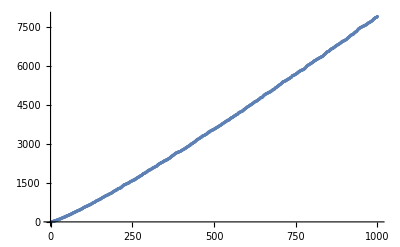

```mathematica
ListPlot[Table[{i,Prime[i]},{i,1,1000}]]
```

```mathematica
FactorInteger[1000000]
```

{{2,6},{5,6}}

```mathematica
2^6*5
```

320

```mathematica
Prime
```

```mathematica
1000000/8
```

```mathematica
125000 * 125000
```

15625000000

```mathematica
Prime[100000]
```

1299709